# Mathematica as a Tool for Astronomy and Physics

## Lecture 14 Wintersemester 2009/10 Markus Röllig

## Fitting

Required Reading:

Curve Fitting
Manipulating Numerical Data
Statistical Model Analysis
Statistical Model Analysis
Curve Fitting & Approximate Functions

### Fit

A common task is to find a formula that bets fits a given set of data. One way to do this in Mathematica is to use Fit.

Fit[data,funs,vars] finds a least-squares fit to a list of data as a linear combination of the functions funs of variables vars. As data we take the distance of the planets in the solar system in astronomical units (AU).

```mathematica
data=AstronomicalData["Planet","SemimajorAxis"]/AstronomicalData["Earth","SemimajorAxis"]
```

{0.3870989,0.7233319,1.,1.5236621,5.2033624,9.5370693,19.191262,30.06896,39.481682}

```mathematica
planets=AstronomicalData["Planet"]
```

{Mercury,Venus,Earth,Mars,Jupiter,Saturn,Uranus,Neptune,Pluto}

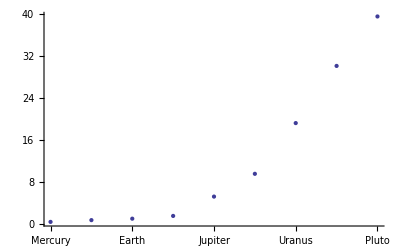

```mathematica
ListPlot[data,Ticks->{MapIndexed[{First@#2,#1}&,planets],Automatic}]
```

Now we use Fit to find the best fitting linear function:

```mathematica
line = Fit[data, {1,x},x]
```

-12.1658+4.813519 x

Plotting both, data and fit reveals the bad quality of the fit. That is simply because the data can not be represented by a line.

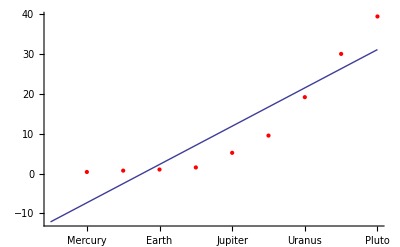

```mathematica
Show[ListPlot[data, PlotStyle->Red,Ticks->{MapIndexed[{First@#2,#1}&,planets],Automatic}], Plot[line, {x, 0, 9}]]
```

We could try higher order functions

```mathematica
parabola = Fit[data, {1,x,x^2}, x]
```

5.2597-4.69127 x+0.950479 x^2

```mathematica
poly3rd= Fit[data, {1,x,x^2,x^3}, x]
```

3.4098-2.9199 x+0.53005 x^2+0.028028 x^3

Each additional order terms improves the overall fit of the data

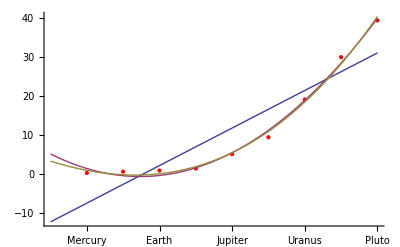

```mathematica
Show[ListPlot[data, PlotStyle->Red,Ticks->{MapIndexed[{First@#2,#1}&,planets],Automatic}], Plot[{line, parabola,poly3rd}, {x, 0, 9}]]
```

The Titius–Bode law (sometimes termed just Bode's law) is a hypothesis that the bodies in some orbital systems, including the Sun's, orbit at semi-major axes in an exponential function of planetary sequence. The hypothesis correctly predicted the orbits of Ceres and Uranus, but failed as a predictor of Neptune's orbit. The law relates the semi-major axis, a, of each planet outward from the Sun in units such that the Earth's semi-major axis is equal to 10, with
a=n+4
where n=0,3,6,12,24,48,...

The resulting values can be divided by 10 to convert them into astronomical units (AU), which would result in the expression
a=0.4+0.3 2^m with m=-∞,0,1,2,....
For the outer planets, each planet is predicted to be roughly twice as far away from the Sun as the previous object.

{0.4,0.7,1.,1.6,2.8,5.2,10.,19.6,38.8,77.2}

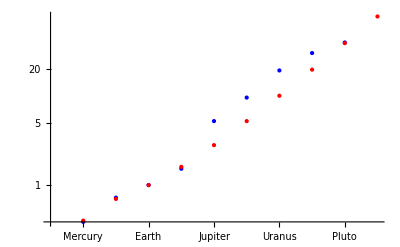

```mathematica
bode=Table[0.4+0.3 2^m,{m,Join[{-∞},Range[0,8]]}]
ListLogPlot[{data,bode},PlotStyle->{Blue,Red},Ticks->{MapIndexed[{First@#2,#1}&,planets],Automatic}]
```

This seems to fit only to till Mars. However, if we would shift all predictions starting from Jupiter to the next outer orbit we would have a match!: Actually, we missed a "planet". Ceres was considered a planet from 1801 until the 1860s, so Bode included Ceres in his sequence:

```mathematica
ceres=AstronomicalData["Ceres","SemimajorAxis"]/AstronomicalData["Earth","SemimajorAxis"]
data=Insert[AstronomicalData["Planet","SemimajorAxis"]/AstronomicalData["Earth","SemimajorAxis"],ceres,5]
```

2.7659561

{0.3870989,0.7233319,1.,1.5236621,2.7659561,5.2033624,9.5370693,19.191262,30.06896,39.481682}

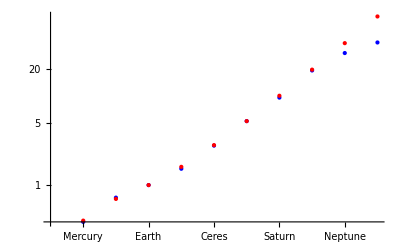

```mathematica
ListLogPlot[{data,bode},PlotStyle->{Blue,Red},Ticks->{MapIndexed[{First@#2,#1}&,Insert[planets,"Ceres",5]],Automatic}]
```

Which is a very good fit, given the fact that Bode developed his sequence in the very early 19th century, long before Neptune and Pluto were discovered!

```mathematica
Clear[data,line,parabola,poly3rd]
```

As another example we simulate real data by adding some random noise to the 'real' values. In this case we simulate the fall of an object from 5m height:

```mathematica
messwerte=Table[{t, -9.81 t^2/2 + 5 +RandomReal[{-0.2,0.2}]},
      {t, 0.1, 0.9, 0.01}];
```

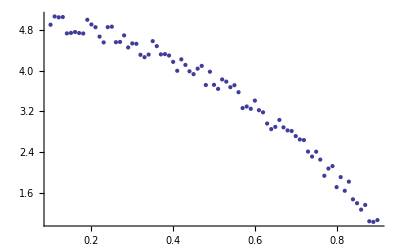

```mathematica
ListPlot[messwerte]
```

Using Fit, we can find the best fitting parameters of the general formula a+b t^2. b is half the gravitational acceleration and a is the starting height.

```mathematica
Fit[messwerte,{1,t^2},{t}]
```

5.00217-4.86614 t^2

To find the result 'by hand' we could perform the sum of squares of the deviations in terms of the unknown position, and then compute the derivatives with respect to these two variables to get a homogeneous linear system of two equations with two unknowns

```mathematica
fehlersumme=Sum[(messwerte[[i,2]]-(g/2 t^2+h)/.{t->messwerte[[i,1]]})^2,{i,Length[messwerte]}];
Short[fehlersumme,10]
fehlersumme=Simplify@fehlersumme
```

(1.05956-0.405 g-h)^2+(1.0238-0.39605 g-h)^2+(1.03612-0.3872 g-h)^2+(1.35776-0.37845 g-h)^2+(1.2652-0.3698 g-h)^2+«72»+(5.05804-0.00845 g-h)^2+(5.05214-0.0072 g-h)^2+(5.06911-0.00605 g-h)^2+(4.90617-0.005 g-h)^2

1114.+3.03503 g^2-570.178 h+81. h^2+g (-64.368+24.678 h)

```mathematica
Solve[{D[fehlersumme, g] == 0, D[fehlersumme, h] == 0}, {g, h}]
(g/2 t^2+h)/.%
```

{{g→-9.73228,h→5.00217}}

{5.00217-4.86614 t^2}

Another way to solve the problem is to use the PseudoInverse. We need to set up the corresponding matrix:

```mathematica
PseudoInverse[{1, First[#]^2/2}& /@ messwerte].
                              (Last /@ messwerte)
```

{5.00217,-9.73228}

As already mentioned, Fit performs a least square minimization.

Fit is not limited to simple polynomia, i.e. functions of powers of x, but can swallow any linear combination of any functions:

```mathematica
data = {{-Pi, 4}, {-Pi/2, 0}, {0, 1}, {Pi/2, -1}, {Pi, -4}};
```

Fit the data to a linear combination of sine functions using machine arithmetic:

```mathematica
Fit[data, {Sin[x/2], Sin[x], Sin[2 x]}, x]
```

-4. Sin[x/2]+2.32843 Sin[x]+0. Sin[2 x]

Show the data with the curve :

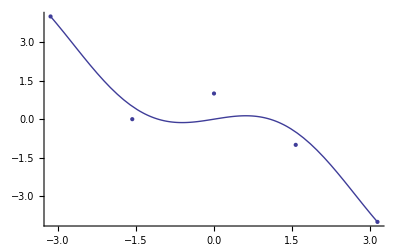

```mathematica
Show[ListPlot[data], Plot[%, {x,-Pi, Pi}],PlotRange->All]
```

You can also do multidimensional fits. Here is data in two dimensions:

```mathematica
data = {{0,0,0}, {1,0, 1}, {0,1,2}, {1,1,0},{1/2,1/2,1}};
```

At first, we will find the plane that fits the data best

```mathematica
plane=Fit[data, {1, x, y}, {x,y}]
Show[Plot3D[plane,  {x,0,1},{y,0,1}, PlotStyle->Opacity[.5], PlotRange->{0,2}], Graphics3D[{Red, PointSize[0.05], Map[Point, data]}]]
```

0.8-0.5 x+0.5 y

-Graphics3D-

Now lets find the quadratic that fits the data best

```mathematica
quad = Fit[data, {1, x, y, x^2, x y, y^2}, {x,y}]
Show[Plot3D[quad,  {x,0,1},{y,0,1}, PlotStyle->Opacity[.5], PlotRange->{0,2}], Graphics3D[{Red, PointSize[0.05], Map[Point, data]}]]
```

7.23065×10^-16+1.76087 x-0.76087 x^2+2.23913 y-3. x y-0.23913 y^2

-Graphics3D-

#### Exercises

Find a linear and quadratic fit to the sequence of the first 20 primes

Take the following data and find a best fitting polynomial

```mathematica
data={{-2.,58.91477567353922},{-1.8,49.122379749189804},{-1.6,33.84316875171661},{-1.4,18.397447574957127},{-1.2,14.124347067895702},{-1.,7.721489914441162},{-0.7999999999999998,4.469593722608596},{-0.5999999999999999,5.107793228179681},{-0.3999999999999999,3.7515285155233666},{-0.19999999999999996,2.592741509664536},{0.,2.},{0.20000000000000018,2.4348819638889423},{0.40000000000000036,1.0110618886513378},{0.6000000000000001,2.3678600966373464},{0.8000000000000003,2.3988988374323936},{1.,0.6046113731685077},{1.2000000000000002,-2.401358338685386},{1.4000000000000004,-2.185297354538078},{1.6,-2.815605658667949},{1.8000000000000003,-5.477201403872526},{2.,-3.8006843749317554}}
```

{{-2.,58.9148},{-1.8,49.1224},{-1.6,33.8432},{-1.4,18.3974},{-1.2,14.1243},{-1.,7.72149},{-0.8,4.46959},{-0.6,5.10779},{-0.4,3.75153},{-0.2,2.59274},{0.,2.},{0.2,2.43488},{0.4,1.01106},{0.6,2.36786},{0.8,2.3989},{1.,0.604611},{1.2,-2.40136},{1.4,-2.1853},{1.6,-2.81561},{1.8,-5.4772},{2.,-3.80068}}

### LinearModelFit

A related but much more powerful variant for linear fits is the function LinearModelFit.

LinearModelFit[{y_1,y_2,…},{f_1,f_2,…},x]constructs a linear model of the form β_0+β_1 f_1+β_2 f_2+⋯ that fits the y_i for successive x values 1, 2, ….
LinearModelFit returns a symbolic FittedModel object to represent the linear model it constructs. The properties and diagnostics of the model can be obtained from model["property"]. Fit a linear function to the following data:

```mathematica
data={{0,1},{1,0},{3,2},{5,4}};
```

```mathematica
lm=LinearModelFit[data,x,x]
```

FittedModel[0.186441+0.694915 x]

```mathematica
FullForm[%]
```

FittedModel[List["Linear",List[0.186441,0.694915],List[List[x],List[1,x]],List[0,0]],List[List[1.,1.,1.,1.]],List[List[0,1],List[1,0],List[3,2],List[5,4]],List[List[1.,0.],List[1.,1.],List[1.,3.],List[1.,5.]],Function[Null,Internal`LocalizedBlock[List[x],Slot[1]],List[HoldAll]]]

To get the functional form use Normal

```mathematica
Normal[lm]
```

0.186441+0.694915 x

lm acts as a fully functional expression. You can calculate the model at any point:

```mathematica
lm[2]
```

1.57627

You can plot the model function

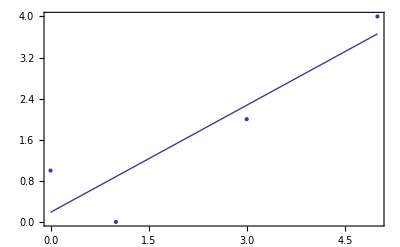

```mathematica
Show[ListPlot[data],Plot[lm[x],{x,0,5}],Frame->True]
```

And you can extract a lot information about the fitting:

```mathematica
lm["FitResiduals"]
```

{0.813559,-0.881356,-0.271186,0.338983}

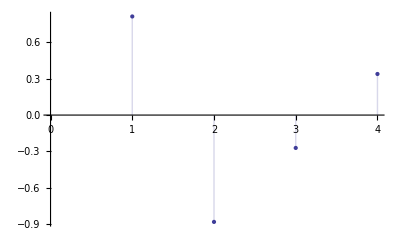

```mathematica
ListPlot[lm["FitResiduals"], Filling->Axis]
```

Obtain an analysis of variance table for the model:

```mathematica
lm["ANOVATable"]
```

| DF | SS | MS | F Statistic | P-Value
x | 1 | 7.12288 | 7.12288 | 8.75521 | 0.0977564
Error | 2 | 1.62712 | 0.813559 |  | 
Total | 3 | 8.75 |  |  |

Here are all possible properties:

```mathematica
lm["Properties"]
```

{AdjustedRSquared,AIC,ANOVATable,ANOVATableDegreesOfFreedom,ANOVATableEntries,ANOVATableFStatistics,ANOVATableMeanSquares,ANOVATablePValues,ANOVATableSumsOfSquares,BetaDifferences,BestFit,BestFitParameters,BIC,CatcherMatrix,CoefficientOfVariation,CookDistances,CorrelationMatrix,CovarianceMatrix,CovarianceRatios,Data,DesignMatrix,DurbinWatsonD,EigenstructureTable,EigenstructureTableEigenvalues,EigenstructureTableEntries,EigenstructureTableIndexes,EigenstructureTablePartitions,EstimatedVariance,FitDifferences,FitResiduals,Function,FVarianceRatios,HatDiagonal,MeanPredictionBands,MeanPredictionConfidenceIntervals,MeanPredictionConfidenceIntervalTable,MeanPredictionConfidenceIntervalTableEntries,MeanPredictionErrors,ParameterConfidenceIntervals,ParameterConfidenceIntervalTable,ParameterConfidenceIntervalTableEntries,ParameterConfidenceRegion,ParameterErrors,ParameterPValues,ParameterTable,ParameterTableEntries,ParameterTStatistics,PartialSumOfSquares,PredictedResponse,Properties,Response,RSquared,SequentialSumOfSquares,SingleDeletionVariances,SinglePredictionBands,SinglePredictionConfidenceIntervals,SinglePredictionConfidenceIntervalTable,SinglePredictionConfidenceIntervalTableEntries,SinglePredictionErrors,StandardizedResiduals,StudentizedResiduals,VarianceInflationFactors}

#### Exercises

Use LinearNodelFit to find a linear model for the first 100 primes.

Visualize the data together with the plot.

Visualize the residuals. Any systematic trends in the residuals hints towards violations in the assumptions of independent normal errors. Is a linear model a reasonable assumptions for the prime distribution?

### FindFit

FindFit[data,expr,pars,vars] finds numerical values of the parameters pars that make expr give a best fit to data as a function of vars. The data can have the form {{x_1,y_1,…,f_1},{x_2,y_2,…,f_2},…}, where the number of coordinates x, y, … is equal to the number of variables in the list vars. The data can also be of the form {f_1,f_2,…}, with a single coordinate assumed to take values 1, 2, ….

Again we take a look at a list of primes:

```mathematica
Table[{x,Prime[x]},{x,20}]
```

{{1,2},{2,3},{3,5},{4,7},{5,11},{6,13},{7,17},{8,19},{9,23},{10,29},{11,31},{12,37},{13,41},{14,43},{15,47},{16,53},{17,59},{18,61},{19,67},{20,71}}

And try to find the best-fit parameters a, b, and c:

```mathematica
FindFit[%,a x Log[b+c x],{a,b,c},x]
```

{a→1.42076,b→1.65558,c→0.534645}

The result is given as replacement rules. This makes it easy to insert the found parameters and evaluate the fitted function

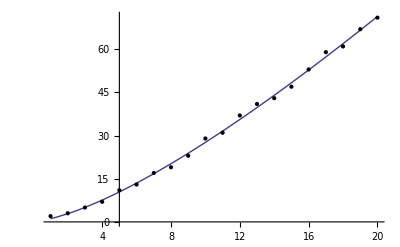

```mathematica
Plot[a x Log[b+c x]/.%,{x,1,20},Epilog->Point@%%]
```

You can also do constrained fitting. FindFit[data,{expr,cons},pars,vars] finds a best fit subject to the parameter constraints cons.

```mathematica
model=a  Cos[ω t];
```

```mathematica
data=Table[{t,Cos[2.1 t]},{t,0,10,.25}]+RandomReal[.1,41];
```

Fit to the model with positive amplitude and frequency between 1 and 2:

```mathematica
fit=FindFit[data,{model,{a>0,1<ω<2}},{a,ω},t]
```

{a→0.855057,ω→2.}

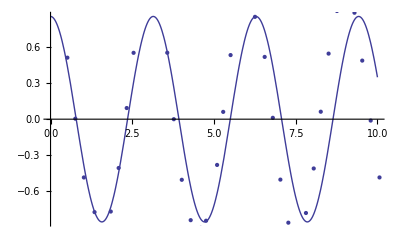

```mathematica
Show[Plot[model/.fit,{t,0,10}],ListPlot[data,PlotRange->All]]
```

In this case, the residuals are not distributed normally, indicating that the frequency constraint is too strict.

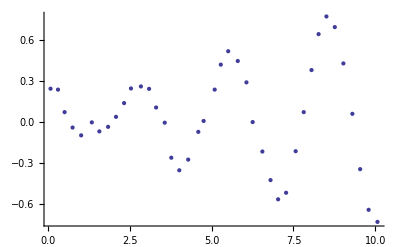

```mathematica
residuals=Apply[Function[{t,y},Evaluate[{t,y-model/.fit}]],data,1];
ListPlot[residuals,PlotRange->All]
```

Like all functions that start with Find, FindFit also depends on a reasonable starting point for the parameters it is trying to fit. Consider the following model and data

```mathematica
model=a Exp[-b (x-c)^2]+d Sin[ω x+ϕ];
data=Table[{x,model/.{a->2,b->1,c->0,d->2,ω->0.67,ϕ->0.1}},{x,-5,5,.1}]+RandomReal[.25,101];
```

Per default all parameters start with 1:

```mathematica
f1=FindFit[data,model,{a,b,c,d,ω,ϕ},x]
```

{a→3.09107,b→0.355948,c→3.66956,d→2.13644,ω→0.89277,ϕ→0.830846}

Searching with a better starting value for the parameter c:

```mathematica
f2 = FindFit[data, model, {a, b, {c, 0}, d, ω, ϕ}, x]
```

{a→2.18262,b→0.705781,c→0.122859,d→1.98384,ω→0.66775,ϕ→-0.060311}

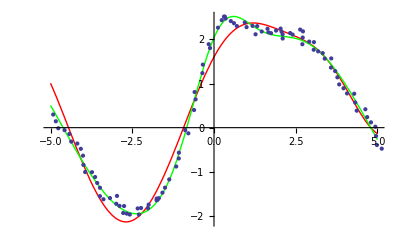

```mathematica
Show[Plot[Evaluate[model/.{f1,f2}],{x,-5,5},PlotStyle->{Red,Green}],ListPlot[data,PlotRange->All]]
```

Like any other fitting function we can also fit multivariate data.

```mathematica
model=a Exp[-b ((x-x0)^2+(y-y0)^2)];
data=MapThread[{#1[[1]],#1[[2]],1.2 Exp[-34((#1-.56).(#1-.56))]+#2}&,{RandomReal[1,{100,2}],RandomReal[{-.1,.1},100]}];
```

```mathematica
fit=FindFit[data,model,{a,b,{x0,.5},{y0,.6}},{x,y}]
```

{a→1.16501,b→32.3776,x0→0.573298,y0→0.55446}

```mathematica
Show[Plot3D[model/.fit,{x,0,1},{y,0,1},PlotRange->All],ListPointPlot3D[data,PlotStyle->Directive[PointSize[Medium],Red]]]
```

-Graphics3D-

#### Exercises

Fit the following data to a model of exponential decay (a Exp[-k t] ) and show the data together with the fit.

```mathematica
data={{1.0,12.},{1.9,10.},{2.6,8.2},{3.4,6.9},{5.0,5.9}};
```

Calculate and plot the residuals.

Use a linear fit on the logarithm of the data for a model of exponential decay.

Fit a model to the following data

```mathematica
data = Import["ExampleData/lubricant.tsv","TSV","HeaderLines"->7];
model=Subscript[θ, 1]/(Subscript[θ, 2]+Subscript[x, 1])+Subscript[θ, 3] Subscript[x, 2]+Subscript[θ, 4] Subscript[x, 2]^2+Subscript[θ, 5] Subscript[x, 2]^3+(Subscript[θ, 6]+Subscript[θ, 7] Subscript[x, 2]^2)Subscript[x, 2] Exp[(-Subscript[x, 1])/(Subscript[θ, 8]+Subscript[θ, 9] Subscript[x, 2]^2)];
```

Try to fit the following data to the function cos(a x+b x^2+c)

```mathematica
data = Table[{x, Cos[1.2 x + 0.00023 x^2 + 0.345]} // N, 
             {x, 0, 2Pi, 2Pi/60}];
```

### NonlinearModelFit

FindFit gives the parameter estimates:

```mathematica
data=Table[{i,Exp[RandomReal[{i-1,i}]]},{i,10}];
```

```mathematica
FindFit[data,Exp[a +b x],{a,b},x]
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{a→2.58331,b→0.660727}

NonlinearModelFit allows for extraction of additional information about the fitting:

```mathematica
nlm=NonlinearModelFit[data,Exp[a+b x],{a,b},x]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

FittedModel[ⅇ^(2.58331+«1»)]

Extract the parameter estimates:

```mathematica
nlm["BestFitParameters"]
```

{a→2.58331,b→0.660727}

```mathematica
nlm[{"BestFit","FitResiduals","ParameterTable"}]
```

{ⅇ^(2.58331+0.660727 x),{-24.207,-42.8298,-78.7894,-160.117,-276.686,-361.842,-883.323,-1427.6,2529.58,-763.961}, | Estimate | Standard Error | t Statistic | P-Value
a | 2.58331 | 1.34255 | 1.92418 | 0.0905303
b | 0.660727 | 0.138953 | 4.75505 | 0.00143591}

Extract additional results and diagnostics:

NonlinearModelFit[{y_1,y_2,…},form,{β_1,…},x] constructs a nonlinear model with structure form that fits the y_i for successive x values 1, 2, … using the parameters β_1,….

NonlinearModelFit[data,{form,cons},{β_1,…},{x_1,…}]constructs a nonlinear model subject to the parameter constraints cons.

#### Exercises 1

Take the following data:

```mathematica
data={{25.,0.001},{25.5,0.002},{26.,0.011},{26.5,0.045},{27.,0.112},{27.5,0.215},{28.,0.259},{28.5,0.206},{29.,0.112},{29.5,0.044},{30.,0.011}};
```

Plot the data and determine which model function could be used to fit the data

Find a best fitting model

Visualize the result and assess the quality of your fit.

#### Exercises 2

Find a fit for the following data

```mathematica
data={{2.6974467862489533,0.97229404548603},{5.618912450260353,0.34408835321208553},{11.958537198367395,0.767091752560637},{7.022357111131001,0.46070405106676504},{4.13019854701156,0.9473461758009301},{7.482735762962925,1.211159784744381},{11.332242013763953,0.43991944610730394},{10.906651148623197,0.6750847777587251},{12.072757256755946,1.1779790966132409},{2.479992498977854,0.9611157405440809},{6.326165225521667,0.720895822674964},{5.889772736449281,1.1866350858382821},{8.638087401152873,0.6059355128802886},{11.230407994424755,0.8111384694425021},{11.001943177063623,0.86141389816221},{8.653076221372515,0.6706464342941485},{4.268350256440161,0.7705350677043583},{9.269184707255565,0.3652880938009757},{3.0430928100337624,0.6495434423575803},{9.861498808610996,0.5511572773253413}}
```

{{2.69745,0.972294},{5.61891,0.344088},{11.9585,0.767092},{7.02236,0.460704},{4.1302,0.947346},{7.48274,1.21116},{11.3322,0.439919},{10.9067,0.675085},{12.0728,1.17798},{2.47999,0.961116},{6.32617,0.720896},{5.88977,1.18664},{8.63809,0.605936},{11.2304,0.811138},{11.0019,0.861414},{8.65308,0.670646},{4.26835,0.770535},{9.26918,0.365288},{3.04309,0.649543},{9.8615,0.551157}}

Visualize the result and assess the quality of your fit.

### Application: Automatic fitting to many datasets

In the following application we have a set of data files, each containing a single Gaussian peak. We will fit a Gaussian to each file.

```mathematica
model = a1 Exp[-(b1(x-x1))^2] ;
```

```mathematica
SetDirectory["\home"] (* change to data directory *)
```

Let us first try our routine on a smaller sample:

{{a1→1.58053,b1→-7.36043,x1→0.13689}}

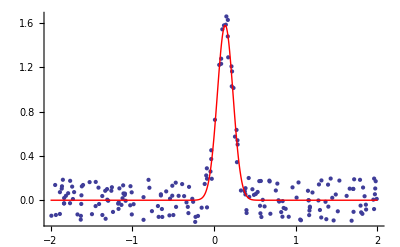

```mathematica
fits = Block[{a1,b1,x1,x,data,model},
Table[
data=Import["data"<>ToString[i]<>".dat"];
model = a1 Exp[-(b1(x-x1))^2] ;
 FindFit[data, model, {a1,b1, x1},x],{i,1,1}]]
Show[ ListPlot[Import["data"<>ToString[1]<>".dat"], PlotRange->All],Plot[Evaluate[model /. fits[[1]]],{x,-2,2}, PlotRange->All, PlotStyle->Directive[Thick,Red]]]
```

Looks good.

```mathematica
fits = Block[{a1,b1,x1,x,data,model},
Table[
data=Import["data"<>ToString[i]<>".dat"];
model = a1 Exp[-(b1(x-x1))^2] ;
 FindFit[data, model, {a1,b1, x1},x],{i,1,9}]]
```

{{a1→1.58053,b1→-7.36043,x1→0.13689},{a1→1.12123,b1→4.34843,x1→0.836494},{a1→0.577834,b1→2.99198,x1→0.992224},{a1→2.62291,b1→4.8659,x1→-0.159035},{a1→2.07833,b1→7.83052,x1→0.886974},{a1→1.11627,b1→7.76633,x1→0.397532},{a1→2.23832,b1→4.22257,x1→0.265222},{a1→1.40525,b1→7.90808,x1→0.463375},{a1→0.243065,b1→-3.22391×10^-10,x1→3.8217}}

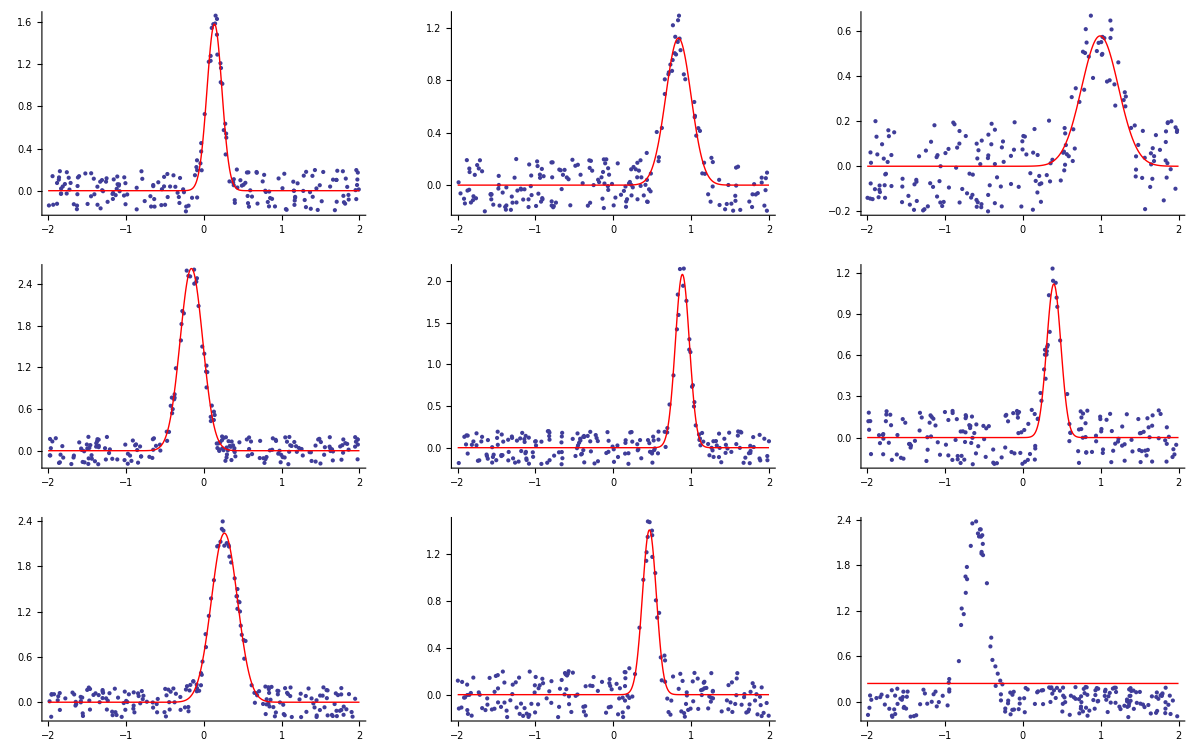

```mathematica
GraphicsGrid@Partition[Table[Show[ ListPlot[Import["data"<>ToString[i]<>".dat"], PlotRange->All],Plot[Evaluate[model /. fits[[i]]],{x,-2,2}, PlotRange->All, PlotStyle->Directive[Thick,Red]]],{i,1,9}],3]
```

The last fit looks bad. Maybe we should provide a reasonable starting point?

{{a1→2.40798,b1→5.18147,x1→-0.60557}}

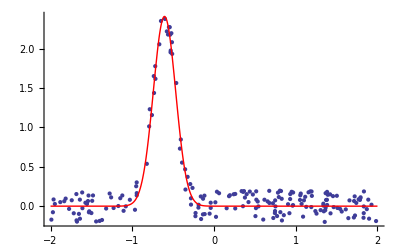

```mathematica
fits = Block[{a1,b1,x1,x,data,model},
Table[
data=Import["data"<>ToString[i]<>".dat"];
model = a1 Exp[-(b1(x-x1))^2] ;
 FindFit[data, model, {a1,b1,{ x1,-1}},x],{i,9,9}]]
Show[ ListPlot[Import["data"<>ToString[9]<>".dat"], PlotRange->All],Plot[Evaluate[model /. fits[[1]]],{x,-2,2}, PlotRange->All, PlotStyle->Directive[Thick,Red]]]
```

This looks better. But we had to look at the data and provide the fit by hand. How could we do it automatically? We could for example search the maximum data point and hope that this is the peak?

```mathematica
peakguess=#[[Position[#,Max[#[[All,2]]]][[1,1]],1]]&@Import["data"<>ToString[9]<>".dat"]
```

-0.600618

Using the guess:

{{a1→1.58053,b1→7.36043,x1→0.13689},{a1→1.12123,b1→4.34843,x1→0.836494},{a1→0.577834,b1→2.99198,x1→0.992224},{a1→2.62291,b1→4.8659,x1→-0.159035},{a1→2.07833,b1→7.83052,x1→0.886974},{a1→1.11627,b1→7.76633,x1→0.397532},{a1→2.23832,b1→4.22257,x1→0.265222},{a1→1.40525,b1→7.90808,x1→0.463375},{a1→2.40798,b1→5.18147,x1→-0.60557}}

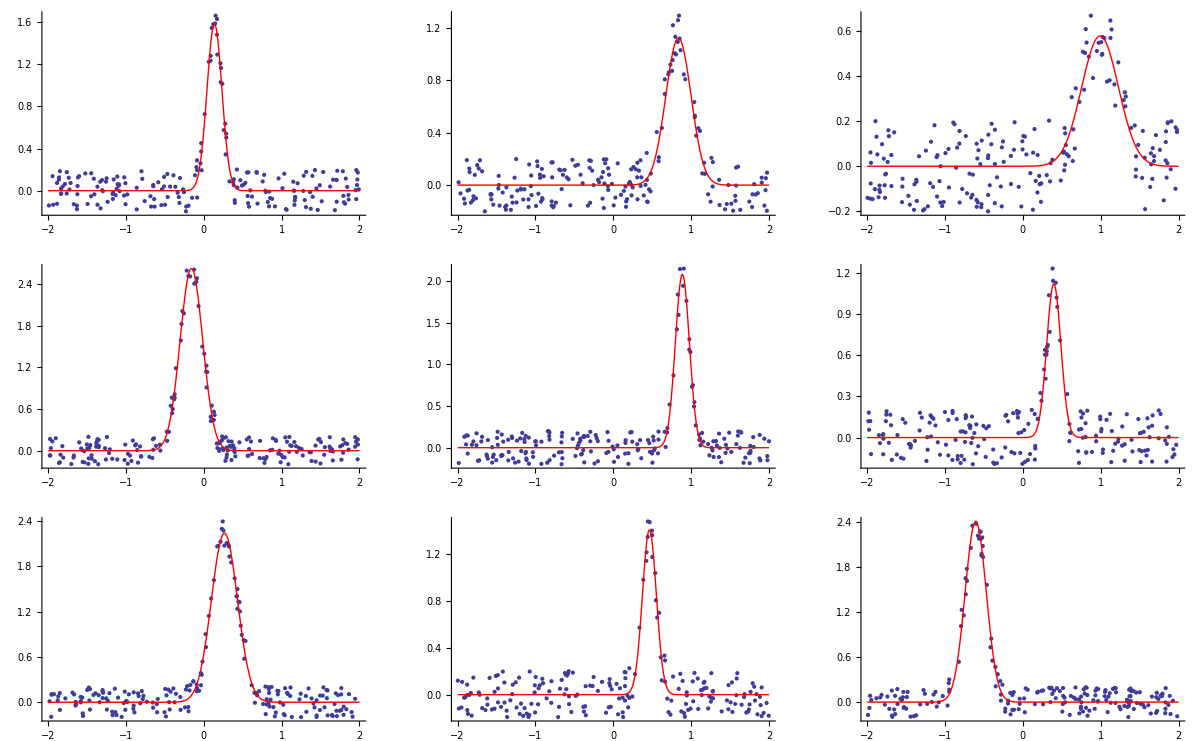

```mathematica
fits = Block[{a1,b1,x1,x,data,model,peakguess},
Table[
data=Import["data"<>ToString[i]<>".dat"];
peakguess=#[[Position[#,Max[#[[All,2]]]][[1,1]],1]]&@data;
model = a1 Exp[-(b1(x-x1))^2] ;
 FindFit[data, model, {a1,b1, {x1,peakguess}},x],{i,1,9}]]
GraphicsGrid@Partition[Table[Show[ ListPlot[Import["data"<>ToString[i]<>".dat"], PlotRange->All],Plot[Evaluate[model /. fits[[i]]],{x,-2,2}, PlotRange->All, PlotStyle->Directive[Thick,Red]]],{i,1,9}],3]
```

With more than just a few fits it is also difficult to actually spot an faulty fit. We need a quantitative quality number to assess the fit quality and to immediately notice if something goes wrong. Let us calculate the residuals for all data fits, the RMS.

```mathematica
residuals=Table[data=Import["data"<>ToString[j]<>".dat"];Table[{data[[i,1]],data[[i,2]]-a1 Exp[-(b1(data[[i,1]]-x1))^2]/.fits[[j]]},{i,1,Length@data}],{j,1,numberoffiles}];
rms=√(Total[(#[[All,2]])^2]/Length[#])&/@residuals
resMax=Max[#[[All,2]]]&/@residuals
```

{0.10933,0.116762,0.113124,0.11454,0.114623,0.116647,0.117497,0.114214,0.593845,0.320233,0.114976,0.11569,0.120818,0.447532,0.115102,0.250962,0.120005,0.314471,0.50802,0.269856,0.114578,0.111514,0.245766,0.117175,0.17547,0.275661,0.547309,0.118272,0.110989,0.115558,0.113955,0.111656,0.11521,0.476515,0.114464,0.478927,0.182739,0.111757,0.122491,0.329831,0.403734,0.115129,0.119399,0.219678,0.1133,0.418946,0.316462,0.116799,0.273933,0.1212,0.203151,0.345862,0.11356,0.115066,0.11064,0.112568,0.117369,0.110195,0.353321,0.112848,0.288275,0.115415,0.11199,0.116476,0.107051,0.112398,0.461499,0.438631,0.117745,0.113798,0.112006,0.107572,0.113175,0.405577,0.119645,0.330282,0.11522,0.11305,0.115417,0.473083,0.11176,0.588659,0.116977,0.19414,0.112598,0.112442,0.118322,0.562905,0.181818,0.111953,0.29976,0.230163,0.116077,0.249674,0.120626,0.11809,0.204624,0.451596,0.626154,0.111357}

{0.195888,0.199781,0.199853,0.199294,0.198075,0.197248,0.204693,0.203539,2.13369,1.92845,0.193442,0.205633,0.199543,2.40046,0.216274,1.948,0.198793,1.29571,2.29235,1.32228,0.199046,0.198961,1.18058,0.199803,0.716788,1.30118,2.52582,0.205331,0.211994,0.199826,0.193299,0.198229,0.198821,2.12582,0.189575,1.90737,0.659772,0.196805,0.198231,1.71913,1.37297,0.199788,0.199029,0.944827,0.199608,2.22714,1.27399,0.199978,1.33791,0.198883,0.845729,1.37125,0.198025,0.199512,0.197914,0.212804,0.196346,0.230865,2.10992,0.199175,1.05755,0.19964,0.199884,0.200617,0.199145,0.196649,1.43067,1.80186,0.222143,0.207182,0.19965,0.197992,0.199758,1.94,0.199374,1.02527,0.200486,0.198949,0.199018,1.5039,0.189439,2.35656,0.201878,0.884229,0.198575,0.199787,0.199814,2.31223,0.867736,0.197243,1.03764,1.00095,0.230499,1.2463,0.207094,0.199219,1.15018,2.28138,2.54566,0.255829}

-Graphics-

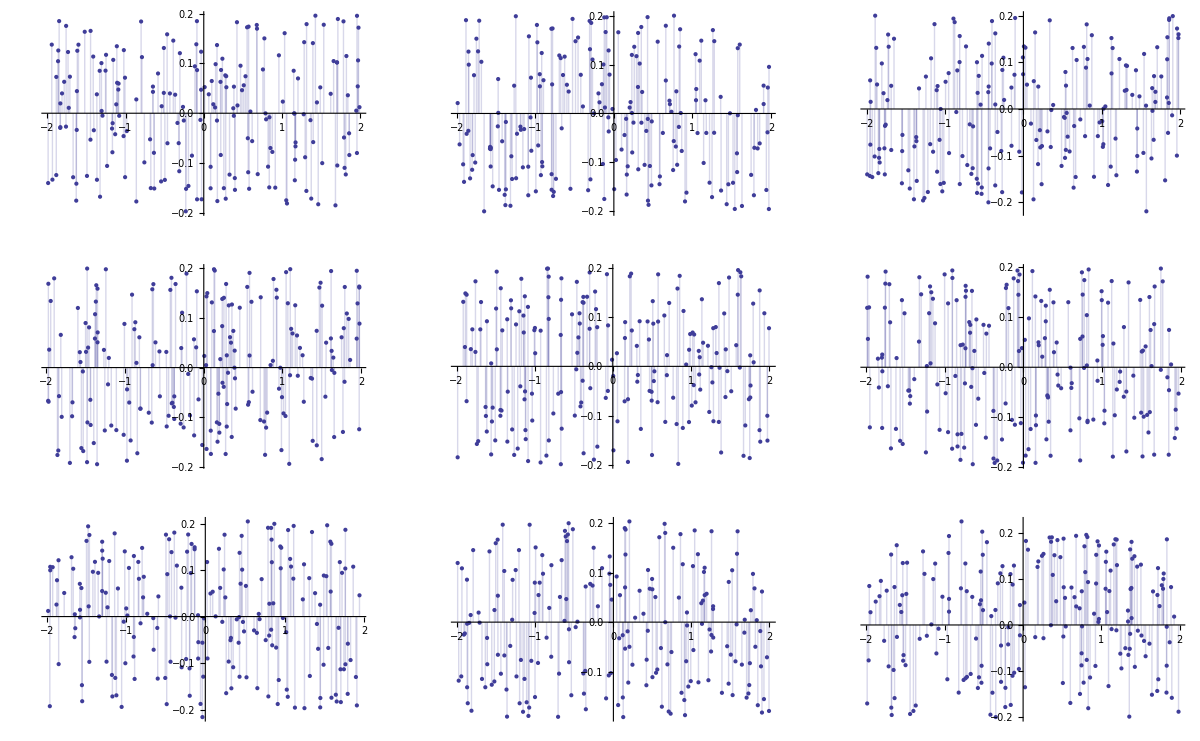

```mathematica
numberoffiles=9;
fits = Block[{a1,b1,x1,x,data,model,peakguess},
Table[
data=Import["data"<>ToString[i]<>".dat"];
peakguess=#[[Position[#,Max[#[[All,2]]]][[1,1]],1]]&@data;
model = a1 Exp[-(b1(x-x1))^2] ;
 FindFit[data, model, {a1,b1, {x1,peakguess}},x],{i,1,numberoffiles}]];
residuals=Table[data=Import["data"<>ToString[j]<>".dat"];Table[{data[[i,1]],data[[i,2]]-a1 Exp[-(b1(data[[i,1]]-x1))^2]/.fits[[j]]},{i,1,Length@data}],{j,1,numberoffiles}];
rms=√(Total[(#[[All,2]])^2]/Length[#])&/@residuals;
resMax=Max[#[[All,2]]]&/@residuals;
GraphicsGrid@Partition[Table[Show[ ListPlot[Import["data"<>ToString[i]<>".dat"], PlotRange->All],Plot[Evaluate[model /. fits[[i]]],{x,-2,2}, PlotRange->All, PlotStyle->Directive[Thick,Red]]],{i,1,numberoffiles}],3]
GraphicsGrid@Partition[Table[ ListPlot[residuals[[i]],Filling->Axis, PlotRange->All],{i,1,numberoffiles}],3]
```

Now we can add a meaningful table.

```mathematica
TableForm[Transpose[{Range[numberoffiles],a1/.fits,1/√b1/.fits,x1/.fits,rms,resMax}],TableHeadings->{None,{"#","Amplitude","σ","Position","RMS","max Residuum"}}]
```

# | Amplitude | σ | Position | RMS | max Residuum
1 | 1.58053 | 0.368594 | 0.13689 | 0.10933 | 0.195888
2 | 1.12123 | 0.47955 | 0.836494 | 0.116762 | 0.199781
3 | 0.577834 | 0.578124 | 0.992224 | 0.113124 | 0.199853
4 | 2.62291 | 0.453334 | -0.159035 | 0.11454 | 0.199294
5 | 2.07833 | 0.357359 | 0.886974 | 0.114623 | 0.198075
6 | 1.11627 | 0.358833 | 0.397532 | 0.116647 | 0.197248
7 | 2.23832 | 0.486644 | 0.265222 | 0.117497 | 0.204693
8 | 1.40525 | 0.355602 | 0.463375 | 0.114214 | 0.203539
9 | 2.40798 | 0.439312 | -0.60557 | 0.11717 | 0.22573

Or with some additional styling and highlighting in case a problem occurs:

```mathematica
table=Table[{
i,
If[(a1/.fits[[i]])<0,Style[NumberForm[a1/.fits[[i]],{3,2}],{Bold,Red}],NumberForm[a1/.fits[[i]],{3,2}]],
If[(1/b1/.fits[[i]])<0,Style[NumberForm[1/b1/.fits[[i]],{3,2}],{Bold,Red}],NumberForm[1/b1/.fits[[i]],{3,2}]],
NumberForm[x1/.fits[[i]],{3,2}],
NumberForm[rms[[i]],{3,2}],
If[resMax[[i]]>(a1/.fits[[i]]),Style[NumberForm[resMax[[i]],{3,2}],{Bold,Red}],
NumberForm[resMax[[i]],{3,2}]]},{i,1,numberoffiles}];
TableForm[table,TableHeadings->{None,{"#","Amplitude","σ","Position","RMS","max Residuum"}},TableAlignments->Center]
```

# | Amplitude | σ | Position | RMS | max Residuum
1 | 1.58 | 0.14 | 0.14 | 0.11 | 0.20
2 | 1.12 | 0.23 | 0.84 | 0.12 | 0.20
3 | 0.58 | 0.33 | 0.99 | 0.11 | 0.20
4 | 2.62 | 0.21 | -0.16 | 0.11 | 0.20
5 | 2.08 | 0.13 | 0.89 | 0.11 | 0.20
6 | 1.12 | 0.13 | 0.40 | 0.12 | 0.20
7 | 2.24 | 0.24 | 0.27 | 0.12 | 0.20
8 | 1.41 | 0.13 | 0.46 | 0.11 | 0.20
9 | 2.41 | 0.19 | -0.61 | 0.12 | 0.23

OK, here the full run on all data files. I deactivated the peak guessing to demonstrate the case sensitive highlighting.

```mathematica
AbsoluteTiming[Quiet[numberoffiles=100;
fits = Block[{a1,b1,x1,x,data,model,peakguess},
Table[
data=Import["data"<>ToString[i]<>".dat"];
peakguess=#[[Position[#,Max[#[[All,2]]]][[1,1]],1]]&@data;
peakguess=1;
model = a1 Exp[-(b1(x-x1))^2] ;
 FindFit[data, model, {a1,b1, {x1,peakguess}},x],{i,1,numberoffiles}]];
residuals=Table[data=Import["data"<>ToString[j]<>".dat"];Table[{data[[i,1]],data[[i,2]]-a1 Exp[-(b1(data[[i,1]]-x1))^2]/.fits[[j]]},{i,1,Length@data}],{j,1,numberoffiles}];
rms=√(Total[(#[[All,2]])^2]/Length[#])&/@residuals;
resMax=Max[#[[All,2]]]&/@residuals;
table=Table[{
i,
If[(a1/.fits[[i]])<0,Style[NumberForm[a1/.fits[[i]],{3,2}],{Bold,Red}],NumberForm[a1/.fits[[i]],{3,2}]],
If[(1/b1/.fits[[i]])<0,Style[NumberForm[1/b1/.fits[[i]],{3,2}],{Bold,Red}],NumberForm[1/b1/.fits[[i]],{3,2}]],
NumberForm[x1/.fits[[i]],{3,2}],
NumberForm[rms[[i]],{3,2}],
If[resMax[[i]]>(a1/.fits[[i]]),Style[NumberForm[resMax[[i]],{3,2}],{Bold,Red}],
NumberForm[resMax[[i]],{3,2}]]},{i,1,numberoffiles}];]]
TableForm[table,TableHeadings->{None,{"#","Amplitude","σ","Position","RMS","max Residuum"}},TableAlignments->Center]
```

{11.57522,Null}

# | Amplitude | σ | Position | RMS | max Residuum
1 | 1.58 | -0.14 | 0.14 | 0.11 | 0.20
2 | 1.12 | 0.23 | 0.84 | 0.12 | 0.20
3 | 0.58 | 0.33 | 0.99 | 0.11 | 0.20
4 | 2.62 | 0.21 | -0.16 | 0.11 | 0.20
5 | 2.08 | 0.13 | 0.89 | 0.11 | 0.20
6 | 1.12 | 0.13 | 0.40 | 0.12 | 0.20
7 | 2.24 | 0.24 | 0.27 | 0.12 | 0.20
8 | 1.41 | 0.13 | 0.46 | 0.11 | 0.20
9 | 0.24 | -3.10×10^9 | 3.82 | 0.59 | 2.13
10 | -0.02 | 1.01 | 3.08 | 0.32 | 1.93
11 | 2.01 | 0.46 | 0.93 | 0.11 | 0.19
12 | 0.73 | 0.26 | 0.65 | 0.12 | 0.21
13 | 0.82 | 0.15 | 0.28 | 0.12 | 0.20
14 | -0.08 | 0.18 | 1.41 | 0.45 | 2.40
15 | 1.37 | 0.20 | 0.15 | 0.12 | 0.22
16 | 4.58 | 0.01 | 1.74 | 0.25 | 1.95
17 | 2.47 | 0.19 | 0.78 | 0.12 | 0.20
18 | 0.22 | 0.04 | 1.70 | 0.31 | 1.30
19 | 0.15 | 7.55×10^8 | 3.57 | 0.51 | 2.29
20 | -0.20 | 0.04 | 1.82 | 0.27 | 1.32
21 | 2.13 | 0.11 | 0.31 | 0.11 | 0.20
22 | 2.54 | 0.36 | -0.36 | 0.11 | 0.20
23 | -0.19 | 0.05 | 1.79 | 0.25 | 1.18
24 | 1.15 | 0.12 | -0.94 | 0.12 | 0.20
25 | 0.13 | 0.06 | 1.94 | 0.18 | 0.72
26 | -0.03 | 0.15 | 1.39 | 0.28 | 1.30
27 | 0.72 | 0.14 | 4.85 | 0.55 | 2.53
28 | 1.64 | 0.28 | 0.48 | 0.12 | 0.21
29 | 2.38 | -0.14 | -0.11 | 0.11 | 0.21
30 | 2.60 | 0.10 | -0.27 | 0.12 | 0.20
31 | 2.04 | 0.20 | 0.52 | 0.11 | 0.19
32 | 1.14 | 0.19 | 0.21 | 0.11 | 0.20
33 | 1.75 | 0.10 | 0.34 | 0.12 | 0.20
34 | 0.14 | -2.11×10^9 | 3.58 | 0.48 | 2.13
35 | 2.07 | 0.42 | 0.51 | 0.11 | 0.19
36 | -0.09 | 0.09 | 1.89 | 0.48 | 1.91
37 | -0.03 | 0.24 | 1.19 | 0.18 | 0.66
38 | 2.57 | 0.10 | 0.77 | 0.11 | 0.20
39 | 1.87 | 0.13 | 0.69 | 0.12 | 0.20
40 | -0.02 | 0.15 | 1.97 | 0.33 | 1.72
41 | 0.19 | 2.50×10^10 | 3.74 | 0.40 | 1.37
42 | 2.10 | -0.18 | 0.17 | 0.12 | 0.20
43 | 1.75 | 0.13 | 0.15 | 0.12 | 0.20
44 | -0.03 | 0.26 | 1.66 | 0.22 | 0.94
45 | 2.65 | 0.11 | 0.76 | 0.11 | 0.20
46 | 0.05 | 0.36 | 1.56 | 0.42 | 2.23
47 | 0.17 | 0.01 | 2.00 | 0.32 | 1.27
48 | 1.00 | 0.09 | 0.82 | 0.12 | 0.20
49 | 0.07 | -3.88×10^9 | 4.26 | 0.27 | 1.34
50 | 2.77 | 0.12 | 0.91 | 0.12 | 0.20
51 | -0.12 | 0.21 | 0.30 | 0.20 | 0.85
52 | -0.10 | 0.13 | 0.47 | 0.35 | 1.37
53 | 2.41 | 0.17 | 0.19 | 0.11 | 0.20
54 | 0.74 | 0.22 | 0.77 | 0.12 | 0.20
55 | 0.69 | 0.22 | 0.86 | 0.11 | 0.20
56 | 0.99 | -0.14 | -0.14 | 0.11 | 0.21
57 | 1.75 | 0.29 | 0.31 | 0.12 | 0.20
58 | 0.66 | 0.18 | 0.61 | 0.11 | 0.23
59 | -0.39 | -0.34 | 5.63 | 0.35 | 2.11
60 | 2.57 | 0.16 | 0.10 | 0.11 | 0.20
61 | 0.13 | -1.01×10^8 | 3.29 | 0.29 | 1.06
62 | 2.19 | 0.15 | 0.19 | 0.12 | 0.20
63 | 1.58 | 0.12 | 0.89 | 0.11 | 0.20
64 | 0.77 | -0.16 | 0.03 | 0.12 | 0.20
65 | 2.53 | 0.12 | 0.28 | 0.11 | 0.20
66 | 1.60 | 0.40 | -0.55 | 0.11 | 0.20
67 | 0.13 | 0.07 | 2.00 | 0.46 | 1.43
68 | -38.30 | 0.00 | 1.88 | 0.44 | 1.80
69 | 1.31 | 0.34 | 0.46 | 0.12 | 0.22
70 | 0.74 | 0.37 | 0.33 | 0.11 | 0.21
71 | 2.65 | 0.13 | 0.66 | 0.11 | 0.20
72 | 2.30 | 0.12 | 0.39 | 0.11 | 0.20
73 | 2.26 | 0.24 | 0.36 | 0.11 | 0.20
74 | 0.50 | 0.01 | 1.99 | 0.41 | 1.94
75 | 2.49 | 0.13 | -0.36 | 0.12 | 0.20
76 | 0.14 | -7.92×10^9 | 3.50 | 0.33 | 1.03
77 | 1.68 | 0.33 | 0.30 | 0.12 | 0.20
78 | 1.45 | 0.15 | 0.23 | 0.11 | 0.20
79 | 2.58 | 0.46 | 0.30 | 0.12 | 0.20
80 | 0.22 | -9.68×10^10 | 3.92 | 0.47 | 1.50
81 | 0.69 | 0.32 | -0.01 | 0.11 | 0.19
82 | -0.51 | 0.03 | 1.89 | 0.59 | 2.36
83 | 1.63 | 0.47 | 0.09 | 0.12 | 0.20
84 | -0.05 | 0.32 | 1.97 | 0.19 | 0.88
85 | 1.16 | 0.15 | 0.19 | 0.11 | 0.20
86 | 2.28 | 0.14 | 0.80 | 0.11 | 0.20
87 | 2.73 | 0.14 | 0.98 | 0.12 | 0.20
88 | 0.17 | -1.19×10^8 | 3.71 | 0.56 | 2.31
89 | 3.29 | 0.00 | 1.91 | 0.18 | 0.87
90 | 1.75 | -0.22 | -0.26 | 0.11 | 0.20
91 | 0.63 | 0.13 | 5.17 | 0.30 | 1.04
92 | -0.10 | 0.08 | 1.20 | 0.23 | 1.00
93 | 2.29 | -0.33 | -0.57 | 0.12 | 0.23
94 | 0.19 | 0.04 | 1.79 | 0.25 | 1.25
95 | 1.39 | 0.11 | 0.68 | 0.12 | 0.21
96 | 1.31 | -0.20 | 0.06 | 0.12 | 0.20
97 | -0.13 | 0.12 | 1.15 | 0.20 | 1.15
98 | 0.11 | -1.57×10^8 | 3.64 | 0.45 | 2.28
99 | -1.11 | -0.30 | 5.34 | 0.63 | 2.55
100 | 1.37 | 0.21 | 0.61 | 0.11 | 0.26

### Data formatting/ Irregular Gridding

Experimental (or other) data that you would like to handle with Mathematica often comes in very different formatting. To fit a function to data you need to provide the data in one of a few forms.

The data can also be of the form {f_1,f_2,…}, with a single coordinate assumed to take values 1, 2, ….

Example:

```mathematica
data={1,2,4,9,16,25,36,49,64}
```

{1,2,4,9,16,25,36,49,64}

The data can have the form {{x_1,y_1,… ,f_1},{x_2,y_2,… ,f_2},…}, where the number of coordinates x,y,… is equal to the number of variables in the list vars.

Example:

```mathematica
data={{1,1},{2,4},{3,9},{4,16},{5,25},{6,36},{7,49},{8,64}}
```

{{1,1},{2,4},{3,9},{4,16},{5,25},{6,36},{7,49},{8,64}}

By default, Mathematica expects the data to be fitted to lie on a regular grid, i.e. all grid lines are equidistant. You can however give explicit coordinates to also fit data on a regular but non-equidistant grid. So far, Mathematica is not able to fit n-dim data on an irregular fit. For example:

```mathematica
regData=Flatten[Table[{i,j,j*i},{i,1,5},{j,1,5}],1];
irrData=Delete[regData,7];
```

The underlying grid in the second set is irregular, i.e. contains 'holes'.

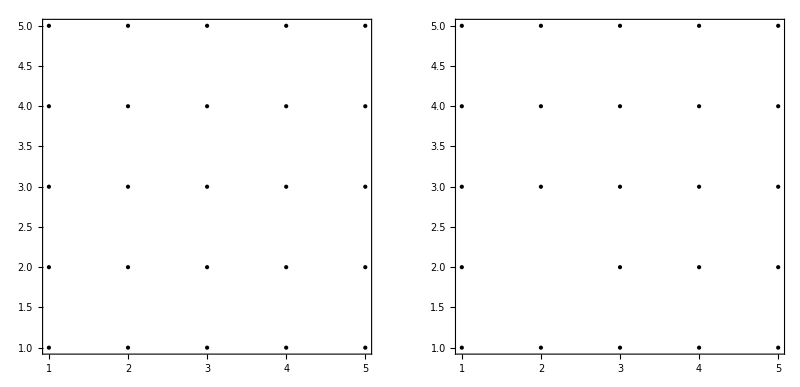

```mathematica
GraphicsRow[{
Graphics[Point@regData[[All,{1,2}]],Frame->True],Graphics[Point@irrData[[All,{1,2}]],Frame->True]}]
```

Mathematica can not interpolate on such holey grids.

```mathematica
regInt=Interpolation[regData]
```

InterpolatingFunction[{{1,5},{1,5}},<>]

```mathematica
irrInt=Interpolation[irrData]
```

Interpolation::indim: The coordinates do not lie on a structured tensor product grid.

Interpolation[{{1,1,1},{1,2,2},{1,3,3},{1,4,4},{1,5,5},{2,1,2},{2,3,6},{2,4,8},{2,5,10},{3,1,3},{3,2,6},{3,3,9},{3,4,12},{3,5,15},{4,1,4},{4,2,8},{4,3,12},{4,4,16},{4,5,20},{5,1,5},{5,2,10},{5,3,15},{5,4,20},{5,5,25}}]

There are several strategies to overcome this limitation.One possibility is of course to fill the hole, either by completing the data with additional measurements or by doing a 'guess' or interpolation by hand:

-Graphics-

We could do a bi-linear interpolation. Assuming, that we would like to know the function value at position P and know the values at the four positions Q

-Graphics-

From Fred Schwab's post on comp.soft-sys.math.mathematica.

"Here's a quick and dirty approach that I sometimes use, which is 
based on a brute-force implementation of Shepard's interpolation 
formula [1]. The suitability, with particular emphasis on graphics 
applications, of this and various other scattered-data interpolation 
methods is discussed in Reference [2]. I chose Shepard's method 
mainly on the basis of its simplicity and because it doesn't tend to 
go "wild" in sparsely sampled regions. In the code below, I've 
selected a weighting exponent alpha=4; see Reference [1] for 
illustrations of the effect of varying this parameter. "
References: 
[1] W. J. Gordon and J. A. Wixom, ``Shepard's method of `metric interpolation' 
to bivariate and multivariate interpolation'', Mathematics of 
Computation, 32 (1978) 253-264. 
[2] R. Franke, ``Scattered data interpolation: tests of some methods'', 
Mathematics of Computation, 38 (1982) 181-200. 
[3] R. J. Renka, ``Multivariate interpolation of large sets of scattered 
data'', ACM Transactions on Mathematical Software, 14 (1988) 139-148. 
[4] ___________, ``Algorithm 660: QSHEP2D: Quadratic Shepard method for 
bivariate interpolation of scattered data'', ibid., 149-150. 
[5] ___________, ``Algorithm 661: QSHEP3D: Quadratic Shepard method for 
trivariate interpolation of scattered data'', ibid., 151-152.

```mathematica
shepard[x_,y_,list_]:=Module[{l,m,alpha=4,w,eps=10.^-16},m=Length[list];
w=Map[((x-#[[1]])^2+(y-#[[2]])^2+eps)^(-alpha/2)&,list];
Sum[list[[l,3]] w[[l]],{l,m}]/Sum[w[[l]],{l,m}]]
```

```mathematica
shepard[2,2,irrData]
```

4.36612

Another way of doing it is to install a supplemental package that provides the desired functionality: http://www.imtek.uni-freiburg.de/simulation/mathematica/IMSweb/.

```mathematica
<<"Imtek`Interpolation`"
```

```mathematica
sp=imsSpline[x,xi,3];
irrInt=imsUnstructuredInterpolation[irrData//N,sp];
```

```mathematica
irrInt[2,2]
regInt[2,2]
```

4.03149

4

You can also use some hidden functionality of Mathematica. Some plot functions do an interpolation inside to fill gaps in provided data sets. ListPlot3D has no problems plotting the holey data set, hence internally it filled the hole up :

```mathematica
ListPlot3D[irrData]
```

-Graphics3D-

Looking at the FullForm shows the existence of a data point at {x,y}={2,2}. We can extract either only the missing point, or the whole re-sampled data set:

```mathematica
ListPlot3D[irrData]//FullForm
```

Graphics3D[GraphicsComplex[List[List[1.,1.,1.],List[1.,2.,2.],List[1.,3.,3.],List[1.,4.,4.],List[1.,5.,5.],List[2.,1.,2.],List[2.,3.,6.],List[2.,4.,8.],List[2.,5.,10.],List[3.,1.,3.],List[3.,2.,6.],List[3.,3.,9.],List[3.,4.,12.],List[3.,5.,15.],List[4.,1.,4.],List[4.,2.,8.],List[4.,3.,12.],List[4.,4.,16.],List[4.,5.,20.],List[5.,1.,5.],List[5.,2.,10.],List[5.,3.,15.],List[5.,4.,20.],List[5.,5.,25.],List[1.25,2.25,3.],List[1.5,2.5,4.],List[1.75,2.75,5.],List[1.25,3.,3.75],List[1.5,3.,4.5],List[1.75,3.,5.25],List[1.25,3.75,4.5],List[1.5,3.5,5.],List[1.75,3.25,5.5],List[1.25,5.,6.25],List[1.5,5.,7.5],List[1.75,5.,8.75],List[2.25,5.,11.25],List[2.5,5.,12.5],List[2.75,5.,13.75],List[1.25,1.75,2.],List[1.5,1.5,2.],List[1.75,1.25,2.],List[1.25,1.,1.25],List[1.5,1.,1.5],List[1.75,1.,1.75],List[2.25,2.75,6.],List[2.5,2.5,6.],List[2.75,2.25,6.],List[1.25,4.,5.],List[1.5,4.,6.],List[1.75,4.,7.],List[1.25,4.75,5.75],List[1.5,4.5,6.5],List[1.75,4.25,7.25],List[2.25,3.,6.75],List[2.5,3.,7.5],List[2.75,3.,8.25],List[3.25,5.,16.25],List[3.5,5.,17.5],List[3.75,5.,18.75],List[2.25,1.25,3.],List[2.5,1.5,4.],List[2.75,1.75,5.],List[2.25,1.,2.25],List[2.5,1.,2.5],List[2.75,1.,2.75],List[3.25,2.,6.5],List[3.5,2.,7.],List[3.75,2.,7.5],List[2.25,3.75,8.25],List[2.5,3.5,8.5],List[2.75,3.25,8.75],List[2.25,4.,9.],List[2.5,4.,10.],List[2.75,4.,11.],List[3.25,2.75,8.75],List[3.5,2.5,8.5],List[3.75,2.25,8.25],List[3.25,3.,9.75],List[3.5,3.,10.5],List[3.75,3.,11.25],List[2.25,4.75,10.5],List[2.5,4.5,11.],List[2.75,4.25,11.5],List[4.25,5.,21.25],List[4.5,5.,22.5],List[4.75,5.,23.75],List[3.25,1.75,5.5],List[3.5,1.5,5.],List[3.75,1.25,4.5],List[3.25,1.,3.25],List[3.5,1.,3.5],List[3.75,1.,3.75],List[4.25,2.,8.5],List[4.5,2.,9.],List[4.75,2.,9.5],List[3.25,3.75,12.],List[3.5,3.5,12.],List[3.75,3.25,12.],List[3.25,4.,13.],List[3.5,4.,14.],List[3.75,4.,15.],List[4.25,2.75,11.5],List[4.5,2.5,11.],List[4.75,2.25,10.5],List[4.25,3.,12.75],List[4.5,3.,13.5],List[4.75,3.,14.25],List[3.25,4.75,15.25],List[3.5,4.5,15.5],List[3.75,4.25,15.75],List[4.25,1.75,7.25],List[4.5,1.5,6.5],List[4.75,1.25,5.75],List[4.25,1.,4.25],List[4.5,1.,4.5],List[4.75,1.,4.75],List[4.25,3.75,15.75],List[4.5,3.5,15.5],List[4.75,3.25,15.25],List[4.25,4.,17.],List[4.5,4.,18.],List[4.75,4.,19.],List[4.25,4.75,20.],List[4.5,4.5,20.],List[4.75,4.25,20.],List[1.,1.25,1.25],List[1.,1.5,1.5],List[1.,1.75,1.75],List[1.,2.25,2.25],List[1.,2.5,2.5],List[1.,2.75,2.75],List[1.,3.25,3.25],List[1.,3.5,3.5],List[1.,3.75,3.75],List[1.,4.25,4.25],List[1.,4.5,4.5],List[1.,4.75,4.75],List[2.,1.25,2.5],List[2.,1.5,3.],List[2.,1.75,3.5],List[2.,2.,4.],List[2.,2.25,4.5],List[2.,2.5,5.],List[2.,2.75,5.5],List[2.,3.25,6.5],List[2.,3.5,7.],List[2.,3.75,7.5],List[2.,4.25,8.5],List[2.,4.5,9.],List[2.,4.75,9.5],List[3.,1.25,3.75],List[3.,1.5,4.5],List[3.,1.75,5.25],List[3.,2.25,6.75],List[3.,2.5,7.5],List[3.,2.75,8.25],List[3.,3.25,9.75],List[3.,3.5,10.5],List[3.,3.75,11.25],List[3.,4.25,12.75],List[3.,4.5,13.5],List[3.,4.75,14.25],List[4.,1.25,5.],List[4.,1.5,6.],List[4.,1.75,7.],List[4.,2.25,9.],List[4.,2.5,10.],List[4.,2.75,11.],List[4.,3.25,13.],List[4.,3.5,14.],List[4.,3.75,15.],List[4.,4.25,17.],List[4.,4.5,18.],List[4.,4.75,19.],List[5.,1.25,6.25],List[5.,1.5,7.5],List[5.,1.75,8.75],List[5.,2.25,11.25],List[5.,2.5,12.5],List[5.,2.75,13.75],List[5.,3.25,16.25],List[5.,3.5,17.5],List[5.,3.75,18.75],List[5.,4.25,21.25],List[5.,4.5,22.5],List[5.,4.75,23.75],List[1.25,2.,2.5],List[1.5,1.75,2.5],List[1.5,2.,3.],List[1.5,2.25,3.5],List[1.75,1.5,2.5],List[1.75,1.75,3.],List[1.75,2.,3.5],List[1.75,2.25,4.],List[1.75,2.5,4.5],List[1.25,2.5,3.25],List[1.25,2.75,3.5],List[1.5,2.75,4.25],List[1.5,4.75,7.],List[1.75,4.5,7.75],List[1.75,4.75,8.25],List[1.25,3.25,4.],List[1.25,3.5,4.25],List[1.5,3.25,4.75],List[1.25,1.25,1.5],List[1.25,1.5,1.75],List[1.5,1.25,1.75],List[2.25,1.5,3.5],List[2.25,1.75,4.],List[2.25,2.,4.5],List[2.25,2.25,5.],List[2.25,2.5,5.5],List[2.5,1.75,4.5],List[2.5,2.,5.],List[2.5,2.25,5.5],List[2.75,2.,5.5],List[2.5,1.25,3.25],List[2.75,1.25,3.5],List[2.75,1.5,4.25],List[1.5,3.75,5.5],List[1.75,3.5,6.],List[1.75,3.75,6.5],List[1.25,4.25,5.25],List[1.25,4.5,5.5],List[1.5,4.25,6.25],List[2.5,4.75,11.75],List[2.75,4.5,12.25],List[2.75,4.75,13.],List[2.5,2.75,6.75],List[2.75,2.5,6.75],List[2.75,2.75,7.5],List[2.25,3.25,7.25],List[2.25,3.5,7.75],List[2.5,3.25,8.],List[3.5,1.75,6.],List[3.75,1.5,5.5],List[3.75,1.75,6.5],List[2.5,3.75,9.25],List[2.75,3.5,9.5],List[2.75,3.75,10.25],List[3.25,2.25,7.25],List[3.25,2.5,8.],List[3.5,2.25,7.75],List[2.25,4.25,9.5],List[2.25,4.5,10.],List[2.5,4.25,10.5],List[3.5,4.75,16.5],List[3.75,4.5,16.75],List[3.75,4.75,17.75],List[3.5,2.75,9.5],List[3.75,2.5,9.25],List[3.75,2.75,10.25],List[3.25,1.25,4.],List[3.25,1.5,4.75],List[3.5,1.25,4.25],List[4.5,1.75,7.75],List[4.75,1.5,7.],List[4.75,1.75,8.25],List[4.25,1.25,5.25],List[4.25,1.5,6.25],List[4.5,1.25,5.5],List[3.25,3.25,10.5],List[3.25,3.5,11.25],List[3.5,3.25,11.25],List[3.5,3.75,13.],List[3.75,3.5,13.],List[3.75,3.75,14.],List[4.25,2.25,9.5],List[4.25,2.5,10.5],List[4.5,2.25,10.],List[3.25,4.25,13.75],List[3.25,4.5,14.5],List[3.5,4.25,14.75],List[4.5,4.75,21.25],List[4.75,4.5,21.25],List[4.75,4.75,22.5],List[4.5,2.75,12.25],List[4.75,2.5,11.75],List[4.75,2.75,13.],List[4.25,3.25,13.75],List[4.25,3.5,14.75],List[4.5,3.25,14.5],List[4.5,3.75,16.75],List[4.75,3.5,16.5],List[4.75,3.75,17.75],List[4.25,4.25,18.],List[4.25,4.5,19.],List[4.5,4.25,19.]],List[List[List[EdgeForm[],GraphicsGroup[List[Polygon[List[List[2,40,188],List[119,118,282],List[41,42,192],List[40,41,189],List[42,6,139],List[199,26,27],List[54,8,149],List[27,7,30],List[197,25,26],List[117,20,114],List[53,54,201],List[83,82,246],List[77,76,243],List[93,15,90],List[34,5,52],List[61,6,64],List[45,6,42],List[139,6,61],List[130,2,25],List[94,16,112],List[124,19,175],List[97,13,160],List[218,62,61],List[47,46,213],List[53,52,225],List[40,2,129],List[110,109,273],List[209,61,62],List[108,22,120],List[110,111,249],List[111,18,173],List[100,13,97],List[120,22,182],List[109,110,248],List[96,21,105],List[106,17,103],List[102,18,111],List[85,19,124],List[33,7,146],List[37,9,82],List[79,12,76],List[32,33,222],List[70,71,239],List[54,53,226],List[31,32,221],List[124,125,275],List[98,97,264],List[49,4,31],List[78,77,244],List[51,8,54],List[71,72,240],List[11,48,217],List[82,83,227],List[84,13,161],List[154,11,63],List[33,32,205],List[214,62,63],List[48,11,155],List[83,84,228],List[72,12,158],List[88,89,236],List[113,112,261],List[55,7,46],List[90,15,164],List[73,8,70],List[58,14,109],List[69,16,78],List[75,13,84],List[57,12,72],List[52,53,200],List[30,7,33],List[46,47,230],List[47,48,231],List[89,90,237],List[72,71,235],List[67,11,88],List[104,103,270],List[89,88,255],List[84,83,247],List[71,70,234],List[42,41,208],List[81,17,99],List[126,125,289],List[114,113,262],List[196,27,26],List[191,26,25],List[188,25,2],List[103,17,169],List[109,14,163],List[121,18,118],List[112,113,257],List[120,119,283],List[76,12,157],List[119,120,285],List[98,99,267],List[118,18,172],List[114,20,176],List[78,16,167],List[76,77,251],List[113,114,258],List[125,124,288],List[97,98,266],List[90,89,256],List[31,4,135],List[99,98,265],List[99,17,170],List[52,5,138],List[46,7,145],List[77,78,252],List[105,104,271],List[41,40,207],List[126,23,185],List[88,11,154],List[220,63,62],List[145,7,27],List[217,63,11],List[111,110,274],List[105,21,179],List[32,31,204],List[48,47,216],List[118,119,284],List[123,23,126],List[82,9,151],List[103,104,278],List[70,8,148],List[112,16,166],List[104,105,279],List[125,126,276]]],Polygon[List[List[175,174,288,124],List[272,100,101,274],List[149,8,73,245],List[233,55,56,235],List[269,94,95,271],List[281,106,107,283],List[242,67,68,244],List[152,10,91,254],List[146,7,55,233],List[167,16,94,269],List[155,11,67,242],List[161,13,100,272],List[245,73,74,247],List[170,17,106,281],List[199,29,28,198],List[263,79,80,265],List[211,210,214,215],List[210,209,62,214],List[251,80,79,76],List[248,59,58,109],List[153,152,254,255],List[212,211,215,216],List[257,95,94,112],List[227,38,37,82],List[200,35,34,52],List[25,188,190,191],List[198,197,26,199],List[204,203,205,32],List[129,128,207,40],List[225,224,226,53],List[188,40,189,190],List[254,91,92,256],List[154,153,255,88],List[151,150,246,82],List[260,115,116,262],List[133,3,28,203],List[136,4,49,224],List[164,15,115,260],List[128,127,206,207],List[287,121,122,289],List[230,56,55,46],List[157,156,243,76],List[239,74,73,70],List[158,12,79,263],List[147,146,233,234],List[173,18,121,287],List[148,147,234,70],List[150,149,245,246],List[156,155,242,243],List[213,212,216,47],List[166,165,261,112],List[206,43,44,208],List[190,189,193,194],List[134,133,203,204],List[26,191,195,196],List[202,36,35,200],List[27,30,29,199],List[169,168,270,103],List[162,161,272,273],List[168,167,269,270],List[189,41,192,193],List[278,107,106,103],List[163,162,273,109],List[266,101,100,97],List[275,86,85,124],List[132,131,197,198],List[200,53,201,202],List[201,54,149,150],List[202,201,150,151],List[194,193,141,142],List[264,263,265,98],List[231,48,155,156],List[270,269,271,104],List[271,95,96,105],List[196,195,143,144],List[288,287,289,125],List[195,194,142,143],List[198,28,3,132],List[151,9,36,202],List[191,190,194,195],List[131,130,25,197],List[27,196,144,145],List[192,42,139,140],List[193,192,140,141],List[172,171,282,118],List[171,170,281,282],List[135,134,204,31],List[208,44,45,42],List[140,139,61,209],List[141,140,209,210],List[205,29,30,33],List[220,219,152,153],List[143,142,211,212],List[221,50,49,31],List[207,206,208,41],List[144,143,212,213],List[215,214,63,217],List[145,144,213,46],List[216,215,217,48],List[62,218,219,220],List[219,66,10,152],List[142,141,210,211],List[274,101,102,111],List[227,83,228,229],List[229,39,38,227],List[138,137,225,52],List[148,8,51,223],List[223,222,147,148],List[222,33,146,147],List[157,12,57,232],List[221,32,222,223],List[163,14,39,229],List[223,51,50,221],List[226,50,51,54],List[228,84,161,162],List[232,57,56,230],List[230,47,231,232],List[229,228,162,163],List[63,220,153,154],List[137,136,224,225],List[203,28,29,205],List[277,87,86,275],List[275,125,276,277],List[250,60,59,248],List[246,245,247,83],List[255,254,256,89],List[259,96,95,257],List[256,92,93,90],List[238,69,68,236],List[166,16,69,238],List[236,89,237,238],List[237,90,164,165],List[234,233,235,71],List[235,56,57,72],List[238,237,165,166],List[236,68,67,88],List[178,21,96,259],List[258,114,176,177],List[257,113,258,259],List[247,74,75,84],List[165,164,260,261],List[218,65,66,219],List[224,49,50,226],List[61,64,65,218],List[127,1,43,206],List[250,249,174,175],List[241,75,74,239],List[251,77,252,253],List[249,111,173,174],List[253,252,168,169],List[169,17,81,253],List[248,110,249,250],List[175,19,60,250],List[252,78,167,168],List[253,81,80,251],List[244,68,69,78],List[243,242,244,77],List[241,240,159,160],List[187,24,87,277],List[277,276,186,187],List[284,119,285,286],List[184,23,123,286],List[286,123,122,284],List[262,116,117,114],List[285,120,182,183],List[265,80,81,99],List[268,102,101,266],List[268,267,171,172],List[172,18,102,268],List[159,158,263,264],List[267,99,170,171],List[160,159,264,97],List[266,98,267,268],List[273,272,274,110],List[174,173,287,288],List[276,126,185,186],List[261,260,262,113],List[259,258,177,178],List[160,13,75,241],List[240,72,158,159],List[239,71,240,241],List[232,231,156,157],List[286,285,183,184],List[279,105,179,180],List[181,22,108,280],List[284,122,121,118],List[282,281,283,119],List[280,108,107,278],List[278,104,279,280],List[283,107,108,120],List[280,279,180,181],List[289,122,123,126]]]]]],List[],List[],List[],List[]],List[List[GrayLevel[0],Line[List[129,2,130,131,132,3,133,134,135,4,136,137,138,5,34,35,36,9,37,38,39,14,58,59,60,19,85,86,87,24,187,186,185,23,184,183,182,22,181,180,179,21,178,177,176,20,117,116,115,15,93,92,91,10,66,65,64,6,45,44,43,1,127,128,129]]],List[Line[List[2,188,190,194,142,211,215,217,11,67,68,69,16,94,95,96,21]],Line[List[129,40,189,193,141,210,214,63,154,88,236,238,166,112,257,259,178]],Line[List[3,28,29,30,7,55,56,57,12,79,80,81,17,106,107,108,22]],Line[List[132,198,199,27,145,46,230,232,157,76,251,253,169,103,278,280,181]],Line[List[4,49,50,51,8,73,74,75,13,100,101,102,18,121,122,123,23]],Line[List[135,31,221,223,148,70,239,241,160,97,266,268,172,118,284,286,184]],Line[List[138,52,200,202,151,82,227,229,163,109,248,250,175,124,275,277,187]],Line[List[176,114,262,260,164,90,256,254,152,219,218,61,139,42,208,206,127]],Line[List[179,105,271,269,167,78,244,242,155,48,216,212,143,195,191,25,130]],Line[List[182,120,283,281,170,99,265,263,158,72,235,233,146,33,205,203,133]],Line[List[185,126,289,287,173,111,274,272,161,84,247,245,149,54,226,224,136]],Line[List[128,207,41,192,140,209,62,220,153,255,89,237,165,261,113,258,177]],Line[List[131,197,26,196,144,213,47,231,156,243,77,252,168,270,104,279,180]],Line[List[134,204,32,222,147,234,71,240,159,264,98,267,171,282,119,285,183]],Line[List[137,225,53,201,150,246,83,228,162,273,110,249,174,288,125,276,186]]],List[Line[List[9,151,150,149,8,148,147,146,7,145,144,143,142,141,140,139,6]],Line[List[36,202,201,54,51,223,222,33,30,27,196,195,194,193,192,42,45]],Line[List[14,163,162,161,13,160,159,158,12,157,156,155,11,154,153,152,10]],Line[List[39,229,228,84,75,241,240,72,57,232,231,48,217,63,220,219,66]],Line[List[43,206,207,40,188,25,197,198,28,203,204,31,49,224,225,52,34]],Line[List[19,175,174,173,18,172,171,170,17,169,168,167,16,166,165,164,15]],Line[List[60,250,249,111,102,268,267,99,81,253,252,78,69,238,237,90,93]],Line[List[64,61,209,210,211,212,213,46,55,233,234,70,73,245,246,82,37]],Line[List[87,277,276,126,123,286,285,120,108,280,279,105,96,259,258,114,117]],Line[List[91,254,255,88,67,242,243,76,79,263,264,97,100,272,273,109,58]],Line[List[115,260,261,112,94,269,270,103,106,281,282,118,121,287,288,124,85]],Line[List[35,200,53,226,50,221,32,205,29,199,26,191,190,189,41,208,44]],Line[List[38,227,83,247,74,239,71,235,56,230,47,216,215,214,62,218,65]],Line[List[59,248,110,274,101,266,98,265,80,251,77,244,68,236,89,256,92]],Line[List[86,275,125,289,122,284,119,283,107,278,104,271,95,257,113,262,116]]],List[],List[]]],Rule[VertexNormals,List[List[-0.57735,-0.57735,0.57735],List[-0.738062,-0.530914,0.416408],List[-0.904534,-0.301511,0.301511],List[-0.910885,-0.326034,0.252962],List[-0.930224,-0.301197,0.209676],List[-0.567268,-0.7219,0.396316],List[-0.80154,-0.523493,0.288944],List[-0.872012,-0.436469,0.221562],List[-0.878972,-0.437224,0.190376],List[-0.301511,-0.904534,0.301511],List[-0.497084,-0.8212,0.280246],List[-0.687612,-0.687612,0.233195],List[-0.783983,-0.58818,0.198529],List[-0.801784,-0.571888,0.173454],List[-0.326034,-0.910885,0.252962],List[-0.436469,-0.872012,0.221562],List[-0.58818,-0.783983,0.198529],List[-0.696097,-0.696097,0.175776],List[-0.723688,-0.672181,0.156359],List[-0.301197,-0.930224,0.209676],List[-0.437224,-0.878972,0.190376],List[-0.571888,-0.801784,0.173454],List[-0.672181,-0.723688,0.156359],List[-0.70014,-0.70014,0.140028],List[-0.755372,-0.53007,0.385277],List[-0.771745,-0.528551,0.353617],List[-0.787144,-0.526357,0.321485],List[-0.883774,-0.359033,0.300063],List[-0.85961,-0.415422,0.297481],List[-0.83215,-0.470348,0.293768],List[-0.887908,-0.377251,0.26325],List[-0.861949,-0.427402,0.27271],List[-0.833115,-0.476231,0.28129],List[-0.919266,-0.335882,0.205265],List[-0.907057,-0.370161,0.200572],List[-0.893617,-0.403965,0.195606],List[-0.861647,-0.47197,0.186572],List[-0.842981,-0.506049,0.182478],List[-0.823012,-0.53938,0.178102],List[-0.699709,-0.582277,0.413957],List[-0.6583,-0.631444,0.409781],List[-0.614063,-0.678085,0.40389],List[-0.57775,-0.616604,0.534794],List[-0.576204,-0.653913,0.490293],List[-0.572706,-0.689073,0.444056],List[-0.738087,-0.608355,0.291774],List[-0.665451,-0.687254,0.291301],List[-0.584669,-0.758641,0.287446],List[-0.902411,-0.354131,0.24545],List[-0.893099,-0.381929,0.237706],List[-0.882962,-0.409387,0.22974],List[-0.91755,-0.335703,0.213084],List[-0.903607,-0.369798,0.216205],List[-0.888417,-0.40341,0.219033],List[-0.776195,-0.566813,0.276123],List[-0.74869,-0.608724,0.262523],List[-0.719124,-0.649046,0.248195],List[-0.78347,-0.597884,0.169442],List[-0.76433,-0.623291,0.165251],List[-0.744393,-0.64807,0.160888],List[-0.551184,-0.748711,0.368276],List[-0.534097,-0.774246,0.339534],List[-0.516048,-0.798431,0.310165],List[-0.506219,-0.775819,0.376625],List[-0.441137,-0.82462,0.354119],List[-0.372661,-0.86769,0.328996],List[-0.482369,-0.834662,0.265817],List[-0.467353,-0.847627,0.251217],List[-0.452048,-0.86008,0.236461],List[-0.833543,-0.503868,0.226544],List[-0.78975,-0.568608,0.230175],List[-0.740963,-0.630051,0.232401],List[-0.85251,-0.475795,0.21644],List[-0.831299,-0.514266,0.210883],List[-0.808435,-0.551765,0.204908],List[-0.6306,-0.740491,0.232415],List[-0.569386,-0.789178,0.230211],List[-0.504482,-0.833161,0.226584],List[-0.664024,-0.713068,0.224959],List[-0.639559,-0.737648,0.216425],List[-0.614262,-0.761302,0.20761],List[-0.857792,-0.476389,0.192992],List[-0.834859,-0.514682,0.195228],List[-0.810232,-0.551983,0.197076],List[-0.717909,-0.679273,0.152299],List[-0.712058,-0.686297,0.148224],List[-0.706134,-0.693253,0.144133],List[-0.455951,-0.846647,0.274405],List[-0.413633,-0.870137,0.267897],List[-0.370276,-0.891577,0.260741],List[-0.307729,-0.906377,0.289455],List[-0.313889,-0.90805,0.277343],List[-0.319992,-0.909553,0.265177],List[-0.4367,-0.873836,0.213786],List[-0.436902,-0.875604,0.205996],List[-0.437077,-0.877316,0.198192],List[-0.740374,-0.641761,0.199972],List[-0.692992,-0.692516,0.20046],List[-0.642142,-0.740042,0.199979],List[-0.763437,-0.61631,0.193202],List[-0.741914,-0.643707,0.187627],List[-0.719454,-0.67032,0.181815],List[-0.552094,-0.810155,0.197081],List[-0.514833,-0.834763,0.195236],List[-0.476505,-0.857726,0.192999],List[-0.584173,-0.788523,0.192282],List[-0.580122,-0.793004,0.18602],List[-0.576027,-0.797424,0.179744],List[-0.777304,-0.604449,0.17447],List[-0.751488,-0.636059,0.175198],List[-0.724397,-0.666635,0.175633],List[-0.403478,-0.888385,0.219039],List[-0.36989,-0.903567,0.216214],List[-0.335773,-0.917523,0.21309],List[-0.319911,-0.915966,0.242206],List[-0.313729,-0.920883,0.231404],List[-0.307491,-0.925637,0.220559],List[-0.66671,-0.724328,0.175634],List[-0.636163,-0.7514,0.1752],List[-0.60453,-0.777241,0.174473],List[-0.690229,-0.703108,0.170949],List[-0.684286,-0.710044,0.166104],List[-0.678269,-0.716905,0.16124],List[-0.711165,-0.685399,0.156437],List[-0.698402,-0.698394,0.156463],List[-0.685405,-0.711159,0.156437],List[-0.620672,-0.568621,0.539849],List[-0.662045,-0.557942,0.500397],List[-0.701243,-0.545353,0.459182],List[-0.786608,-0.477771,0.391129],List[-0.830824,-0.421508,0.363403],List[-0.870257,-0.362584,0.333445],List[-0.906377,-0.307729,0.289455],List[-0.90805,-0.313889,0.277343],List[-0.909553,-0.319992,0.265177],List[-0.915966,-0.319911,0.242206],List[-0.920883,-0.313729,0.231404],List[-0.925637,-0.307491,0.220559],List[-0.600033,-0.701167,0.385129],List[-0.631979,-0.679179,0.373254],List[-0.663012,-0.655975,0.360711],List[-0.693044,-0.631599,0.347524],List[-0.72199,-0.606102,0.333721],List[-0.749771,-0.579543,0.319334],List[-0.77631,-0.551983,0.304396],List[-0.820473,-0.502542,0.272535],List[-0.838549,-0.481032,0.255818],List[-0.855739,-0.458997,0.238817],List[-0.873836,-0.4367,0.213786],List[-0.875604,-0.436902,0.205996],List[-0.877316,-0.437077,0.198192],List[-0.351914,-0.887507,0.297471],List[-0.401455,-0.867893,0.292568],List[-0.449915,-0.845761,0.286819],List[-0.547617,-0.791999,0.269913],List[-0.596396,-0.759897,0.25859],List[-0.643146,-0.725041,0.24633],List[-0.713068,-0.664024,0.224959],List[-0.737648,-0.639559,0.216425],List[-0.761302,-0.614262,0.20761],List[-0.788523,-0.584173,0.192282],List[-0.793004,-0.580122,0.18602],List[-0.797424,-0.576027,0.179744],List[-0.354131,-0.902411,0.24545],List[-0.381929,-0.893099,0.237706],List[-0.409387,-0.882962,0.22974],List[-0.475795,-0.85251,0.21644],List[-0.514266,-0.831299,0.210883],List[-0.551765,-0.808435,0.204908],List[-0.61631,-0.763437,0.193202],List[-0.643707,-0.741914,0.187627],List[-0.67032,-0.719454,0.181815],List[-0.703108,-0.690229,0.170949],List[-0.710044,-0.684286,0.166104],List[-0.716905,-0.678269,0.16124],List[-0.335882,-0.919266,0.205265],List[-0.370161,-0.907057,0.200572],List[-0.403965,-0.893617,0.195606],List[-0.47197,-0.861647,0.186572],List[-0.506049,-0.842981,0.182478],List[-0.53938,-0.823012,0.178102],List[-0.597884,-0.78347,0.169442],List[-0.623291,-0.76433,0.165251],List[-0.64807,-0.744393,0.160888],List[-0.679273,-0.717909,0.152299],List[-0.686297,-0.712058,0.148224],List[-0.693253,-0.706134,0.144133],List[-0.728146,-0.556636,0.399949],List[-0.688381,-0.607237,0.396731],List[-0.717365,-0.581979,0.382998],List[-0.745177,-0.555729,0.368615],List[-0.645595,-0.655523,0.391785],List[-0.676163,-0.631799,0.378991],List[-0.705679,-0.606962,0.365532],List[-0.734065,-0.581068,0.351439],List[-0.761243,-0.554177,0.336744],List[-0.802915,-0.475868,0.358993],List[-0.84585,-0.418691,0.330507],List[-0.818101,-0.473389,0.326516],List[-0.905361,-0.369991,0.208395],List[-0.890207,-0.40362,0.211238],List[-0.891941,-0.403805,0.203428],List[-0.88532,-0.365175,0.287847],List[-0.886698,-0.371248,0.275574],List[-0.860862,-0.421452,0.285123],List[-0.62052,-0.607233,0.496208],List[-0.661245,-0.595773,0.455861],List[-0.618314,-0.643784,0.450811],List[-0.584796,-0.728385,0.357028],List[-0.617541,-0.706767,0.345144],List[-0.649327,-0.683901,0.332646],List[-0.680067,-0.659839,0.319565],List[-0.70968,-0.634636,0.305929],List[-0.568384,-0.754421,0.328312],List[-0.601764,-0.73328,0.316514],List[-0.634148,-0.710872,0.304167],List[-0.550828,-0.7792,0.29906],List[-0.488313,-0.800574,0.347321],List[-0.421663,-0.847027,0.323645],List[-0.469528,-0.823909,0.317359],List[-0.877992,-0.404881,0.255344],List[-0.850639,-0.454435,0.264389],List[-0.867264,-0.432142,0.247196],List[-0.90762,-0.348051,0.234704],List[-0.912667,-0.341908,0.223914],List[-0.898434,-0.375897,0.226976],List[-0.838951,-0.510385,0.18886],List[-0.814553,-0.547824,0.190766],List[-0.818814,-0.543623,0.184441],List[-0.708304,-0.64912,0.277395],List[-0.631711,-0.724661,0.275332],List[-0.676611,-0.688067,0.262226],List[-0.796171,-0.546421,0.259877],List[-0.815297,-0.525429,0.243342],List[-0.769638,-0.588986,0.246483],List[-0.440695,-0.859276,0.259677],List[-0.397899,-0.881889,0.252881],List[-0.425169,-0.871385,0.244784],List[-0.811037,-0.541779,0.220669],List[-0.764426,-0.604724,0.223521],List[-0.786931,-0.578613,0.214351],List[-0.533678,-0.80614,0.255592],List[-0.583178,-0.774696,0.244439],List[-0.519297,-0.819866,0.241145],List[-0.854326,-0.476024,0.208637],List[-0.856087,-0.476221,0.200821],List[-0.833106,-0.514491,0.203062],List[-0.757949,-0.629709,0.170234],List[-0.73114,-0.660517,0.170737],List[-0.737806,-0.654328,0.165821],List[-0.60506,-0.764156,0.223535],List[-0.542135,-0.810793,0.220691],List[-0.578765,-0.786817,0.21436],List[-0.358163,-0.889015,0.285257],List[-0.407642,-0.869079,0.280233],List[-0.364284,-0.890372,0.273012],List[-0.403668,-0.890184,0.211247],List[-0.370039,-0.905339,0.208405],List[-0.40383,-0.891928,0.203435],List[-0.348087,-0.907608,0.234699],List[-0.375956,-0.89841,0.226974],List[-0.341967,-0.912646,0.223912],List[-0.690359,-0.690185,0.216908],List[-0.715826,-0.666401,0.208574],List[-0.666705,-0.715542,0.208577],List[-0.717897,-0.668524,0.194163],List[-0.668743,-0.717693,0.194165],List[-0.69453,-0.694438,0.188107],List[-0.476099,-0.854286,0.208627],List[-0.514602,-0.833039,0.203053],List[-0.476336,-0.856025,0.200813],List[-0.768117,-0.612403,0.186972],List[-0.77274,-0.608449,0.180728],List[-0.74673,-0.639908,0.181419],List[-0.705265,-0.69238,0.152351],List[-0.692384,-0.705261,0.152351],List[-0.699294,-0.699292,0.14825],List[-0.547895,-0.814504,0.190774],List[-0.510458,-0.838905,0.188869],List[-0.543657,-0.81879,0.184447],List[-0.612449,-0.768082,0.186966],List[-0.639978,-0.746671,0.181413],List[-0.608522,-0.772684,0.180723],List[-0.660564,-0.731097,0.170739],List[-0.629758,-0.757908,0.170237],List[-0.65435,-0.737786,0.165824],List[-0.697282,-0.697279,0.16613],List[-0.704261,-0.691376,0.161292],List[-0.691381,-0.704256,0.161292]]]],List[Rule[Axes,True],Rule[BoxRatios,List[1,1,0.4]],Rule[Method,List[Rule["RotationControl","Globe"]]],Rule[PlotRange,List[List[1.,5.],List[1.,5.],List[0.,25.]]],Rule[PlotRangePadding,List[Scaled[0.02],Scaled[0.02],Scaled[0.02]]]]]

```mathematica
lp=ListPlot3D[irrData];
```

```mathematica
resampledDataSet=lp[[1,1]];
irrIntresampled=Interpolation[resampledDataSet]
```

InterpolatingFunction[{{1.,5.},{1.,5.}},<>]

```mathematica
irrIntresampled[2,2]
```

4.

```mathematica
missingDataPoint=First@Cases[lp[[1,1]],{x_/;x==2,y_/;y==2,z_}]
```

{2.,2.,4.}

### Application: Fitting chemical reaction rates

```mathematica
Needs["ErrorBarLogPlots`"]
```

In this example we will show how to influence the outcome of the fitting. Consider experimental data on the reaction rate coefficient of the chemical reaction

CN + CH_3 CH_3 ⟶ C_2 H_5+ HCN     for T∈[185 K, 1140K]

The data is given below

```mathematica
labDat={{185,1.2560224946068678*^-10},{210,1.0943335007930955*^-10},{235,9.99053351847897*^-11},{260,9.413112556523018*^-11},{285,9.066507823633049*^-11},{310,8.87133900831551*^-11},{335,8.780789483760246*^-11},{360,8.765629552806604*^-11},{385,8.806742304950834*^-11},{410,8.89113299746979*^-11},{435,9.009676034670511*^-11},{460,9.15578186611793*^-11},{485,9.324576033680581*^-11},{510,9.512375890408821*^-11},{535,9.716346899735934*^-11},{560,9.934270857525923*^-11},{585,1.0164385900103656*^-10},{610,1.0405273743017904*^-10},{635,1.0655778710418098*^-10},{660,1.0914948605036743*^-10},{685,1.1181990863252889*^-10},{710,1.1456239588709485*^-10},{735,1.173713044796287*^-10},{760,1.20241813284768*^-10},{785,1.231697727493045*^-10},{810,1.261515864007963*^-10},{835,1.2918411677684164*^-10},{860,1.322646100973543*^-10},{885,1.353906354598881*^-10},{910,1.3856003538864118*^-10},{935,1.4177088533352344*^-10},{960,1.4502146027972234*^-10},{985,1.4831020704781125*^-10},{1010,1.5163572117949769*^-10},{1035,1.5499672754273617*^-10},{1060,1.5839206397215427*^-10},{1085,1.6182066740098337*^-10},{1110,1.6528156204940495*^-10},{1135,1.687738493190987*^-10}};
```

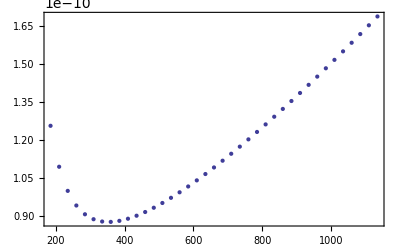

```mathematica
ListPlot[labDat,Frame->True,Axes->False]
```

Plotting the data shows a decline towards lower T values with an incline for T<200K! Usually these reaction rate coefficients are parametrized using the following form:

rate(t)=α (T/(300 K))^β exp(-γ/T)

Directly using NonlinearModelFit to fit the data to the model form we get:

```mathematica
fit=NonlinearModelFit[labDat,(α (T/300.)^β)/ⅇ^(γ/T),{α,β,γ},T]
fit["ParameterTable"]
```

FittedModel[7.19058×10^-15 ⅇ^(«18»/T) T^(«19»)]

| Estimate | Standard Error | t Statistic | P-Value
α | 1.78×10^-11 | 1.12833×10^-27 | 1.57755×10^16 | 1.01572939322672×10^-556
β | 1.37 | 6.5122×10^-17 | 2.10374×10^16 | 3.20976700926279×10^-561
γ | -484. | 1.39869×10^-19 | -3.46038×10^21 | 5.31835260227374×10^-749

Plotting model and data and adding error bars etc. we get the following:

```mathematica
(* assuming 50% errors to the data *)
err=Table[{labDat[[i]],ErrorBar[0.5 labDat[[i,2]],0.5 labDat[[i,2]]]},{i,1,Length@labDat}];
Needs["ErrorBarLogPlots`"]
```

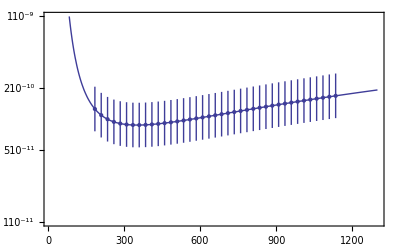

```mathematica
Show[{LogPlot[fit[T],{T,10,1300},Frame->True,Axes->False,PlotRange->{10^-11,10^-9}],ErrorListLogPlot[err]}]
```

This seems to reproduce the lab data nicely. Now imagine additional measurements at low temperature were taken into account and we knew that the reaction rate at 50K was 7×10^-11 cm^3 s^-1.

```mathematica
newDat=Join[{{50.,7. 10^-11}},labDat];
err2=Prepend[Table[{labDat[[i]],ErrorBar[0.5 labDat[[i,2]],0.5 labDat[[i,2]]]},{i,1,Length@labDat}],{{50.,7 10^-11},ErrorBar[0.5 7 10^-11,0.5 7 10^-11]}];
```

```mathematica
fit2=NonlinearModelFit[newDat,(α (T/300.)^β)/ⅇ^(γ/T),{α,β,γ},T]
fit2["ParameterTable"]
```

FittedModel[3.52417×10^-12 ⅇ^(«18»/T) T^(«19»)]

| Estimate | Standard Error | t Statistic | P-Value
α | 7.22384×10^-11 | 5.64599×10^-12 | 12.7946 | 3.72531×10^-15
β | 0.529531 | 0.063348 | 8.35908 | 4.77577×10^-10
γ | -54.0406 | 14.8689 | -3.63448 | 0.000841294

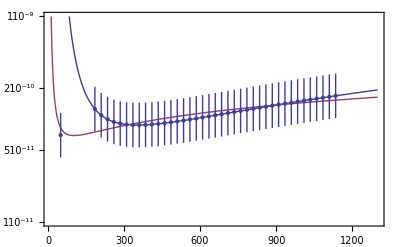

```mathematica
Show[{LogPlot[{fit[T],fit2[T]},{T,10,1300},Frame->True,Axes->False,PlotRange->{10^-11,10^-9}],ErrorListLogPlot[err2]}]
```

We could however, presume that the reaction rates for even lower temperatures will be even smaller. The steep incline in the curve is produced by the negative γ value. We could restrict our fit to positive γ's.

```mathematica
fit3=NonlinearModelFit[newDat,{(α (T/300.)^β)/ⅇ^(γ/T),γ>0},{{α,10^-11},β,γ},T,WorkingPrecision->40]
fit3["ParameterTable"]
Show[{LogPlot[{fit[T],fit2[T],fit3[T]},{T,10,1300},Frame->True,Axes->False,PlotRange->{10^-11,10^-9}],ErrorListLogPlot[err2]}]
```

NonlinearModelFit::precw: The precision of the data and model function (MachinePrecision) is less than the specified WorkingPrecision (40).

NonlinearModelFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 513 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {9.828959820878327`*^-9, 0.00011910158121462154`, 9.92824224331144`*^-9}, is returned.

FittedModel[-5.34151×10^-8 ⅇ^(-«68»/T) T^(«68»)]

FittedModel::precw: The precision of the argument function (MachinePrecision) is less than WorkingPrecision (40).

FittedModel::constr: The property values ParameterTable assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t Statistic | P-Value
α | -5.372066998669899111602343919763241977487×10^-8 | 3.01465×10^-8 | -1.78199 | 0.08296
β | 0.001000000039783696540243718153817553684348 | 0.501194 | 0.00199524 | 0.998419
γ | 0.001008271143900206024204835308921701653162 | 103.942 | 9.7003×10^-6 | 0.999992

-Graphics-

This obviously fails. We need to find a reasonable initial condition for our three parameter:

```mathematica
Clear[f];
f[t_?NumericQ,a_?NumericQ,b_?NumericQ,g_?NumericQ]:=(10^-a(t/300.)^b)/ⅇ^(g/t);
Manipulate[Show[{LogPlot[f[T,a,β,γ],{T,10,1300},Frame->True,Axes->False,PlotRange->{10^-11,10^-9}],ErrorListLogPlot[err2]}],{{a,11},9,13},{{β,0.5},-1,1},{{γ,-54},-100,1000}]
```

After playing around with the sliders we presume the following initial conditions:
α->10^-9.9, β->0.12, γ->15

NonlinearModelFit::precw: The precision of the data and model function (MachinePrecision) is less than the specified WorkingPrecision (40).

FittedModel[1.11685×10^-11 ⅇ^(-«83»/T) T^(«83»)]

FittedModel::precw: The precision of the argument function (MachinePrecision) is less than WorkingPrecision (40).

FittedModel::constr: The property values ParameterTable assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t Statistic | P-Value
α | 9.059745580414755829500248586416816780138×10^-11 | 9.70241×10^-12 | 9.33763 | 2.87177×10^-11
β | 0.3670073822369366173486974014248234900569 | 0.0802977 | 4.57059 | 0.0000527007
γ | 0.3246424946070056870769301952968495820671 | 25.6574 | 0.012653 | 0.989973

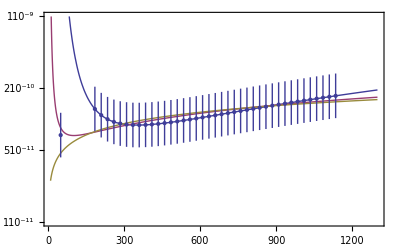

```mathematica
fit3=NonlinearModelFit[newDat,{(α (T/300.)^β)/ⅇ^(γ/T),γ>0,α>0},{{α,10^-9.985},{β,0.12},{γ,15}},T,WorkingPrecision->40]
fit3["ParameterTable"]
Show[{LogPlot[{fit[T],fit2[T],fit3[T]},{T,10,1300},Frame->True,Axes->False,PlotRange->{10^-11,10^-9}],ErrorListLogPlot[err2]}]
```

Our final parameter estimates would be α=9.1×10^-11,β=0.367,γ=0.33.

### Application: χ^2-fit

Another way of determining a best fit model is to minimize a χ^2, i.e the squared difference between theoretical and experimental data point. Let's reuse the chemical reaction rate data and define a chi-square figure

```mathematica
Clear[chi2];
chi2[α_,β_,γ_]:=Total@Table[((newDat[[i,2]]-f[newDat[[i,1]],α,β,γ])/(0.5 newDat[[i,2]]))^2,{i,1,Length[newDat]}]
```

```mathematica
Off[NMinimize::"precw"];
min=NMinimize[
{chi2[α,β,γ],13>α>9,-1≤β≤2,0≤γ≤100},
{{α,11,12},{β,0,1},{γ,0,10}}, 
AccuracyGoal->20,
PrecisionGoal->18,(*Method->{"SimulatedAnnealing","PerturbationScale"->3,"BoltzmannExponent"->Function[{i,df,f0},-df/(Exp[i/10])]}*)(*Method->{"DifferentialEvolution", "ScalingFactor"->1}*)
(*Method->{"RandomSearch","SearchPoints"->100}*)
Method->{"SimulatedAnnealing"(*,"InitialPoints"->inpoints[[All,2;;6]]*)}];
```

```mathematica
min
```

{2.66603,{α→10.0358,β→0.301955,γ→0.}}

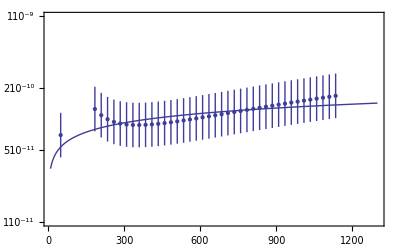

```mathematica
Show[{LogPlot[f[T,α,β,γ]/.min[[2]],{T,10,1300},Frame->True,Axes->False,PlotRange->{10^-11,10^-9}],ErrorListLogPlot[err2]}]
```

Again we were able to find a solution to our minimization problem.

See the documentation for Constrained Optimization for more info.

### Exercises

#### 1

Fit the curve  y=c x^a  to the data points  (1.0, 1.1), (2.0, 2.8),(3.0, 5.2),(4.0, 8.0),(5.0, 11.1).

#### 2

Die folgenden Daten über die Bevölkerung der USA stammen vom US Census Bureau (www.census.gov):

```mathematica
daten={{1790,3929214},{1800,5308483},{1810,7239881},{1820,9638453},{1830,12860702},{1840,17063353},{1850,23191876},{1860,31443321},{1870,38558371},{1880,50189209},{1890,62979766},{1900,76212168},{1910,92228496},{1920,106021537},{1930,123202624},{1940,132164569},{1950,151325798},{1960,179323175},{1970,203302031},{1980,226542199},{1990,248709873}};
daten//TableForm
```

1790 | 3929214
1800 | 5308483
1810 | 7239881
1820 | 9638453
1830 | 12860702
1840 | 17063353
1850 | 23191876
1860 | 31443321
1870 | 38558371
1880 | 50189209
1890 | 62979766
1900 | 76212168
1910 | 92228496
1920 | 106021537
1930 | 123202624
1940 | 132164569
1950 | 151325798
1960 | 179323175
1970 | 203302031
1980 | 226542199
1990 | 248709873

Im Jahre 1940 versuchte Pearl, der Wiederentdecker der logistischen Differentialgleichung, das Bevölkerungswachstum in den USA durch die logistische Funktion, also die Lösung der logistischen Differentialgleichung zu beschreiben. Ihm standen die folgenden Daten zur Verfügung:

Diese Daten sind durch eine Funktion

x(t)=(K C e^(a(t-1790)))/(1+C e^(a(t-1790))) mit Konstanten a,K,C>0 ,

also einer Lösung einer logistischen Differentialgleichung

ẋ=a x (1-x/K)

möglichst gut zu approximieren.

#### 3

Find both the "exponential fit" and "power fit" for the data points  (1.0, 2.0),(2.0, 4.0),(3.0, 8.0),(4.0, 13.0),(5.0, 21.0).

Discuss which curve fits the data best.

## Interpolation

Required Reading:

Approximate Functions and Interpolation
(Guide) Curve Fitting & Approximate Functions

Fitting and Interpolating data is closely related.

### InterpolatingPolynomial

InterpolatingPolynomial[{f_1,f_2,…},x]constructs an interpolating polynomial in x which reproduces the function values f_i at successive integer values 1,2,… of x.

The more general form is InterpolatingPolynomial[{{{x_1,…},f_1,df_1,…},…},{x,…}]which constructs an interpolating polynomial in the variable var with the property that at each point x_i, it matches the function value f_i, the value of the first derivative f'_i, etc., up to the n_ith derivative f_i^(n_i), for i=1,…,m. The interpolating polynomial is written in a form that is very convenient for further numerical calculations. The degree of the polynomial is k-1, where k=n_1+n_2+⋯+n_m+m is the total number of individual data.

```mathematica
InterpolatingPolynomial[{{-1,4},{0,2},{1,6}},x]
```

4+(1+x) (-2+3 x)

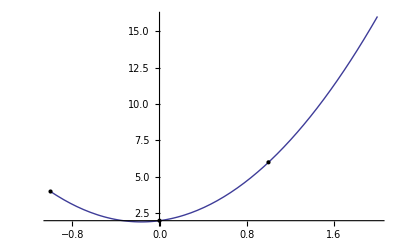

```mathematica
Plot[%,{x,-1,2},Epilog->Point@{{-1,4},{0,2},{1,6}}]
```

Here is another example:

4+(3+(-4+(19/6-35/24 (-4+x)) (-3+x)) (-2+x)) (-1+x)

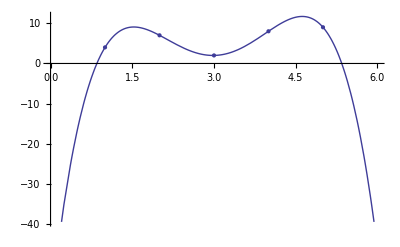

```mathematica
InterpolatingPolynomial[{4,7,2,8,9},x]
Show[Plot[%,{x,0,6}],ListPlot[{4,7,2,8,9}]]
```

By specifying an explicit value for the derivative we can influence the result. Now we fit the same data but want the polynomial to have derivative 0 at x-value 8:

4+(3+(-4+(19/6+(-107/36+109/72 (-4+x)) (-4+x)) (-3+x)) (-2+x)) (-1+x)

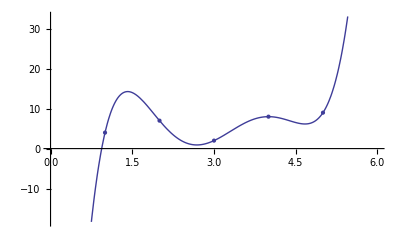

```mathematica
InterpolatingPolynomial[{4,7,2,{8,0},9},x]
Show[Plot[%,{x,0,6}],ListPlot[{4,7,2,8,9}]]
```

You can also find a polynomial in 2 dimensions

```mathematica
InterpolatingPolynomial[{{{0,0},1},{{1,0},7},{{0,1},10},{{2,1},40},{{3,3},151},{{1,2},47}},{x,y}]
```

1+x (2+4 x+5 y)+y (3+6 y)

Now, let us consider the function f(x)=2 arctan(8x). Like (cos(π x/2))^2, it is a smooth function on the interval {-1,1}. But the function 2 arctan(8x) has a singularity near the interval {-1,1}. As a result, of this singularity, we encounter the so-called Runge phenomena—near ±1 the convergence of the interpolating polynomial to the original function breaks down.

```mathematica
n = 40;
f[x_] := 2 ArcTan[8 x]/Pi;
data = Table[{x, f[x]}, {x, -1, 1, 2/n}];
```

```mathematica
ipo[x_] = InterpolatingPolynomial[data // N, x];
```

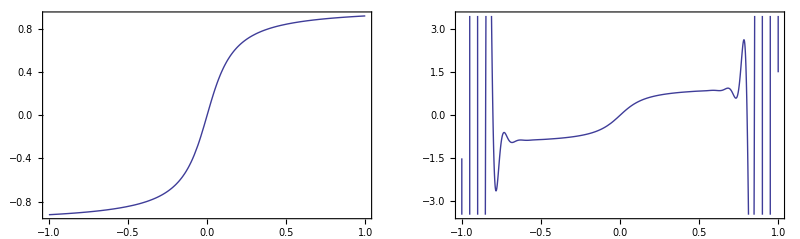

```mathematica
GraphicsRow[
Plot[#, {x, -1, 1}, Frame -> True, Axes -> False,
     DisplayFunction -> Identity]& /@ {f[x], ipo[x]}]
```

One can avoid the Runge phenomena by using non-equidistant x-values.

Another nice feature is to have Mathematica find a polynomial without specifying e.g. function values at the boundaries but only the derivatives. Make the polynomial have zero derivative at -1 and 1 without specifying the values there:

```mathematica
InterpolatingPolynomial[{{-1,Automatic,0},{0,1,1},{1,Automatic,0}},x]
```

1+x (1-x^2/3)

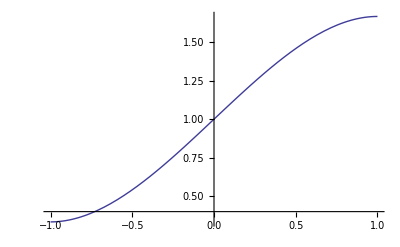

```mathematica
Plot[%,{x,-1,1}]
```

### InterpolatingFunction

While InterpolatingPolynomial allows interpolating data with polynomials (the whole set with one polynomial!) a much more versatile Mathematica function for fitting and interpolation is InterpolatingFunction.

InterpolatingFunction[domain,table]represents an approximate function whose values are found by interpolation. This means, InterpolatingFunction is actually the result of a successful interpolation. To solve an interpolation problem for given data, an InterpolatingFunction-object is produced as follows.

Interpolation[{{x_1,f_1},{x_2,f_2},…}]constructs an interpolation of the function values f_i corresponding to x values x_i.

```mathematica
f=Interpolation[{1,2,3,5,8,5}]
```

InterpolatingFunction[{{1,6}},<>]

We can apply the function to find interpolated values:

```mathematica
f[2.3]
```

2.2545

```mathematica
InputForm[f]
```

InterpolatingFunction[{{1, 6}}, {3, 1, 0, {6}, {4}, 0, 0, 0, 
  0}, {{1, 2, 3, 4, 5, 6}}, {{1}, {2}, {3}, {5}, {8}, {5}}, 
 {Automatic}]

We can plot the interpolation function:

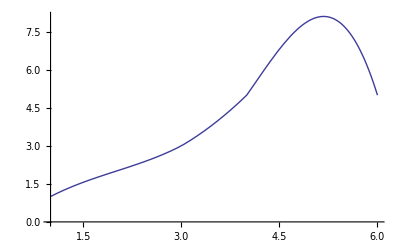

```mathematica
Plot[f[x],{x,1,6}]
```

However, if we leave the original data domain we will get an error and Mathematica tries to extrapolate the result.

```mathematica
f[7]
```

InterpolatingFunction::dmval: Input value {7} lies outside the range of data in the interpolating function. Extrapolation will be used.

-11

An interpolation function will ALWAYS go through the data points.

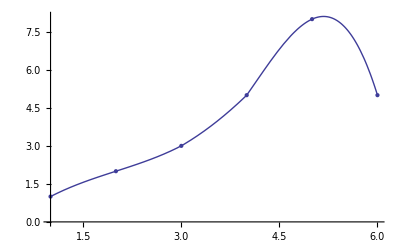

```mathematica
Show[%%,ListPlot[{1,2,3,5,8,5}]]
```

Interpolation forms a piecewise polynomial interpolation as can be seen by comparing the interpolation together with its derivative. The interpolation function will always be continuous, but may not be differentiable:

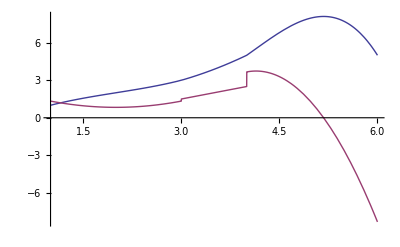

```mathematica
Plot[{f[x],f'[x]},{x,1,6}]
```

One option for Interpolation is the InterpolationOrder. The default setting is InterpolationOrder->3. :

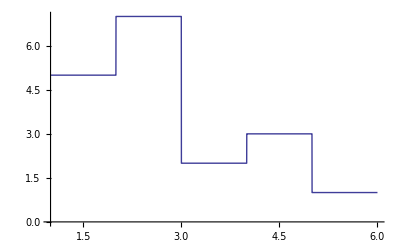

```mathematica
Plot[Interpolation[{1,5,7,2,3,1},InterpolationOrder->0][x],{x,1,6}]
```

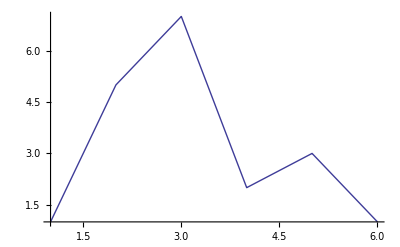

```mathematica
Plot[Interpolation[{1,5,7,2,3,1},InterpolationOrder->1][x],{x,1,6}]
```

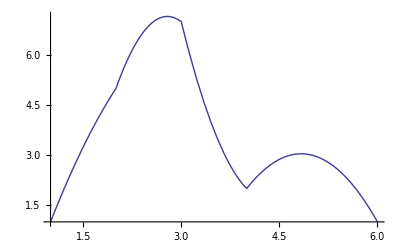

```mathematica
Plot[Interpolation[{1,5,7,2,3,1},InterpolationOrder->2][x],{x,1,6}]
```

With the default choice of order, at least 4 points are needed in each dimension:

```mathematica
Interpolation[{1,2,4}]
```

Interpolation::inhr: Requested order is too high; order has been reduced to {2}.

InterpolatingFunction[{{1,3}},<>]

Interpolation supports a Method option. Possible settings include "Spline" for spline interpolation and "Hermite" for Hermite interpolation.

```mathematica
data = Transpose[{Range[0,10]/10,RandomReal[1,11]}];
```

```mathematica
sp = Interpolation[data, Method->"Spline"]
```

InterpolatingFunction[{{0.,1.}},<>]

```mathematica
he = Interpolation[data, Method->"Hermite"]
```

InterpolatingFunction[{{0.,1.}},<>]

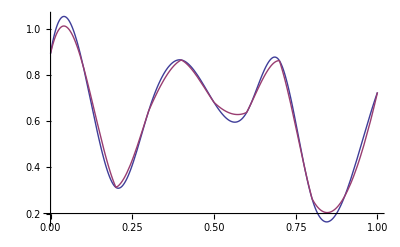
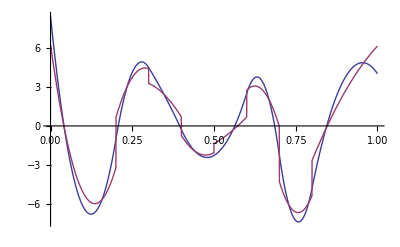

```mathematica
Row[{Plot[{sp[x],he[x]},{x,0,1},PlotRange->All],
Plot[{sp'[x],he'[x]},{x,0,1},PlotRange->All]}]
```

You can also make the interpolation a periodic function:

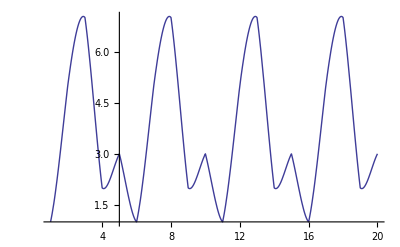

```mathematica
Plot[Interpolation[{1,5,7,2,3,1},PeriodicInterpolation->True][x],{x,1,20}]
```

The data to be interpolated can contain symbolic entities. (This is similar to the InterpolatingPolynomial case.)

```mathematica
Clear[a, α, interp];
interp[a_] = Interpolation[{{1, 1}, {2, 4}, {3, 9}, {4, 16}, 
                        {5, a}, 
                        {6, 36}, {7, 49}, {8, 64}, {9, 81}, {10, 100}}]
```

InterpolatingFunction[{{1,10}},<>]

Here, the resulting interpolating function as a function of a is shown. We plot over the x-range {-1, 11}. All data were contained in the range {1, 10}. Outside, the last domain extrapolation is used and a warning message is issued.

```mathematica
Plot3D[ipo[a][x], {x, -1, 11}, {a, 0, 50}, 
      PlotPoints -> 50]
```

-Graphics3D-

When repeatedly interpolating in a calculation, it is often advantageous to change the interpolation points to prevent the rise of numerical artifacts.

### ListInterpolation

Another function to interpolate a list of data points is ListInterpolation.

ListInterpolation[array]constructs an InterpolatingFunction object which represents an approximate function that interpolates the array of values given. ListInterpolation[array] assumes grid lines at integer positions in each direction.

ListInterpolation[array,{{x_min,x_max},{y_min,y_max},…}]specifies the domain of the grid from which the values in array are assumed to come. You can replace {x_min,x_max} etc. by explicit lists of positions for grid lines. The grid lines are otherwise assumed to be equally spaced.

```mathematica
f=ListInterpolation[{1,2,3,5,8,5}]
```

InterpolatingFunction[{{1,6}},<>]

```mathematica
Plot[f[x],{x,1,6}]
```

-Graphics-

Construct an approximate function with the x values equally spaced on the interval [0,1]:

```mathematica
g=ListInterpolation[{1,2,3,5,8,5},{{0,1}}]
```

InterpolatingFunction[{{0,1}},<>]

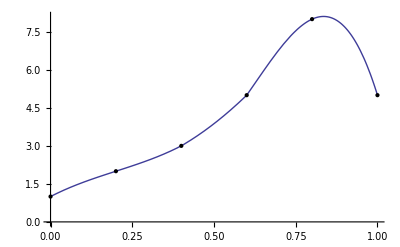

```mathematica
Plot[g[x],{x,0,1},Epilog->MapIndexed[Point[{(#2[[1]]-1)/5,#1}]&,{1,2,3,5,8,5}]]
```

Construct an approximate function that interpolates the values from an array of values:

```mathematica
f=ListInterpolation[Table[Sin[x y],{x,0,1,.25},{y,0,2,.25}],{{0,1},{0,2}}]
```

InterpolatingFunction[{{0.,1.},{0.,2.}},<>]

```mathematica
Show[{Plot3D[f[x,y],{x,0,1},{y,0,2}],Graphics3D[{Red,PointSize[0.03],Table[Point[{x,y,Sin[x y]}],{x,0,1,.25},{y,0,2,.25}]}]}]
```

-Graphics3D-

If you want to interpolate on arbitrary grid points, you can explicitly specify them:

```mathematica
f=ListInterpolation[{0,.3,.6,-.2,3},{{0,.1,.5,1,2}}]
```

InterpolatingFunction[{{0.,2.}},<>]

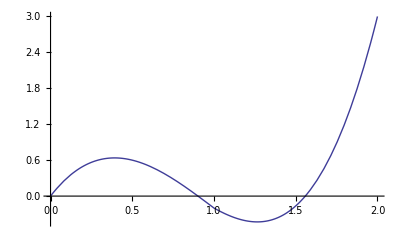

```mathematica
Plot[f[x],{x,0,2}]
```

The x values may be included in the data directly :

```mathematica
Plot[ListInterpolation[{{{0},0},{{0.1},0.3},{{0.5},0.6},{{1},-0.2},{{2},3}}][x],{x,0,2}]
```

-Graphics-

### FunctionInterpolation

If you have a  function (not data points) that you would like to interpolate this can be conveniently done with  FunctionInterpolation[expr,{x,x_min,x_max}]which evaluates expr with x running from x_min to x_max and constructs an InterpolatingFunction object which represents an approximate function corresponding to the result. Mathematica chooses the underlying griding points to optimize accuracy of the fit (non-equidistant, etc.)

```mathematica
sinInterp=FunctionInterpolation[Sin[2 x],{x,0,5}]
```

InterpolatingFunction[{{0.,5.}},<>]

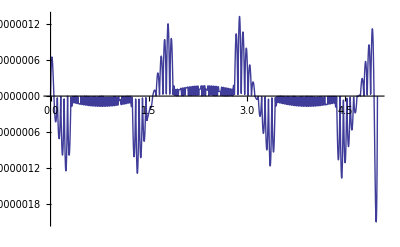

```mathematica
Plot[Evaluate[sinInterp[x] - Sin[2x]], {x, 0, 5}, PlotRange -> All]
```

About 150 points were used to approximate the function sin(2x).

```mathematica
sinInterp[[3,1]]//Length
```

151

When plotting the third derivative we nicely see the discrete sampling:

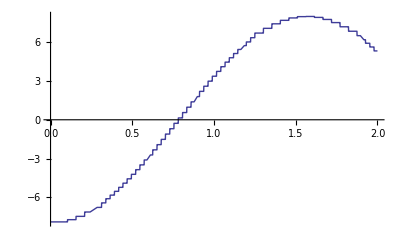

```mathematica
Plot[Evaluate[sinInterp'''[x]], {x, 0, 2}, PlotRange -> All]
```

The use of FunctionInterpolation is recommended when the calculation of a function takes a relatively long time and function values are repeatedly used.  One such function is FresnelC

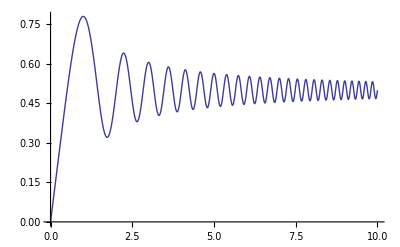
{1.529,-Graphics-}

```mathematica
Plot[FresnelC[x], {x, 0, 10}, PlotRange -> All] // Timing
```

Over 2000 points are needed for the generation of this pot:

```mathematica
%[[2,1,1,3,2,1]]//Length
```

2166

To achieve a six-digit interpolation, we only need about half as many points.

```mathematica
(fipFresnelC = FunctionInterpolation[FresnelC[x], {x, 0, 10},
                                     MaxRecursion -> 8]) // Timing
```

{1.467,InterpolatingFunction[{{0.,10.}},<>]}

```mathematica
fipFresnelC[[3, 1]] // Length
```

1048

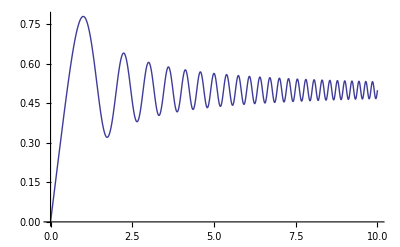
{0.031,-Graphics-}

```mathematica
Plot[fipFresnelC[x], {x, 0, 10}, PlotRange -> All] // Timing
```

One important application is to use FunctionInterpolation to generate a single InterpolatingFunction object from an expression containing several such objects.

### Exercises

Interpolate the sinc(x) function in the interval (-50,50). Remember that sinc(x)=sin(x)/x. Visualize the precision of your interpolation.

Interpolate the  Airy function in the interval (-100, 50). Visualize the precision of your interpolation.

## Links to Untouched Topics

### Parallel Computing

Parallel Computing
Parallel Computing Tools User Guide

### Contexts and Packages

Contexts
Contexts and Packages
Setting Up Mathematica Packages

### Image Processing

Image Processing & Analysis
Image Processing
Image Filtering & Neighborhood Processing
Mathematical Morphology

### MathLink

Introduction to MathLink
MathLink API
How MathLink Is Used
MathLink and External Program Communication

### Statistics

Statistics
Basic Statistics
Statistical Model Analysis

### Random Number Generation

### Compile

Compiling Mathematica Expressions

### Sound and Sonification

Sound
The Representation of Sound
Sound and Sonification

### Signal Processing

### Binary Data

Binary Data
Binary Files

### Databases

DatabaseLink User Guide
Database Connectivity
Using the Example Databases

### Notebook Programming

Notebooks and Documents
Low-Level Notebook Programming
Document Generation

### Splines

Splines

### Automatic Report Generation (SendMail, Twitter, etc.)

Sending Email
Twitter

### Intervals

Interval Arithmetic

### Notation, Symbolize, etc.

Notation Package
Notation, Symbolize and InfixNotation